# Finite temperature string simulations: WHAM analysis

## (with unbiased averages and selection of string iterations)

## © 2017-2024 Alexander Soudackov, Yale University

## String II, Fig S2 (right) and Fig S3 (middle) in the SI to the paper: [Probing Nonadiabaticity of Proton-Coupled Electron Transfer in Ribonucleotide Reductase]

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/souda/Documents/Mathematica/Notebooks/wham-string-simulations/wham-binless

## Constants and conversion factors

### Unit conversions

```mathematica
bohr2a=QuantityMagnitude@UnitConvert[Quantity[1,"BohrRadius"],"Angstroms"];
a2bohr=1/bohr2a;
au2kcal=QuantityMagnitude[UnitConvert[Quantity[1,"Hartrees"],"kilocalories"]×Entity["PhysicalConstant","AvogadroConstant"]["Value"]];
kcal2au=1/au2kcal;
ev2kcal=QuantityMagnitude[UnitConvert[Quantity[1,"ElectronVolts"],"kilocalories"]×Entity["PhysicalConstant","AvogadroConstant"]["Value"]];
kcal2ev=1/ev2kcal;
ev2cm=QuantityMagnitude@UnitConvert[Quantity[1,"ElectronVolts"]/(Entity["PhysicalConstant","PlanckConstant"]["Value"]×Entity["PhysicalConstant","SpeedOfLight"]["Value"]),"wavenumbers"];
cm2ev=1/ev2cm;
au2ev=QuantityMagnitude@UnitConvert[Quantity[1,"Hartrees"],"ElectronVolts"];
ev2au=1/au2ev;
au2cm=QuantityMagnitude@UnitConvert[Quantity[1,"Hartrees"]/(Entity["PhysicalConstant","PlanckConstant"]["Value"]×Entity["PhysicalConstant","SpeedOfLight"]["Value"]),"wavenumbers"];
cm2au=1/au2cm;
```

### Universal constants

Boltzmann constant

```mathematica
kbau=QuantityMagnitude@UnitConvert[Entity["PhysicalConstant","BoltzmannConstant"]["Value"],"Hartrees/K"]
kbkcal=kbau×au2kcal
```

3.1668115635×10^-6

0.0019872042586

Set absolute temperature (in Kelvins):

```mathematica
T=300.;
β=1/(kbkcal*T);
kT=1/β
```

0.596161

## Data and biased distributions

### Parameters (allows variable number of images in each string iteration):

Number of coordinates:

```mathematica
ncoord=3;
```

List of folders with string iterations:

```mathematica
iterations=Range[0,30]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}

Iterations to include in the WHAM analysis (e.g. last 30):

```mathematica
iterationsSelected=Take[iterations,-30]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}

Number of iterations in the final data set:

```mathematica
niter=Length[iterationsSelected]
```

30

In this variant we set the equal number of bins for each coordinate to simplify the generation of all histograms.
(The alternative is to set the binwidth for all coordinates. Some code modification will be required then which is easy)

```mathematica
(* binwidth=0.05; *)
numbins=20;
```

Assumes that the data files are in subdirectories of the directory where this notebook resides

```mathematica
datadir="./";
```

### Read sampling data for each coordinate in each window (last nimages windows comprise the final string)

data file names:
	- sampling data for each iteration is in subfolder with the name “N”, where N is the iteration number in the original simulation setup;
	- within each “iteration” subfolder there are as many “distperframeXX.dat” files as there are images (nimages, can be different for different iterations);
	- each ‘distperframeXX.dat” file contains sampling data with ncoord columns: {r_1, r_2, ..., r_ncoord}, where ncoord is number of coordinates;

Read sampling data for all windows (images of all iterations):

```mathematica
nsamples={};
nimages={};
Block[{iwin,iter,filelist,image,icoord,filedata,dataraw},
dataraw={};
iwin=0;
For[iter=1,iter<niter+1,iter++,
(*filelist=FileNames["distperframe*.dat",ToString[iter]];*)
filelist=Sort[FileNames["distperframe*.dat",ToString[iterationsSelected⟦iter⟧]],ToExpression[StringTake[#1,{StringPosition[#1,"frame"]⟦1,-1⟧+1,StringPosition[#1,"."]⟦1,1⟧-1}]]<ToExpression[StringTake[#2,{StringPosition[#2,"frame"]⟦1,-1⟧+1,StringPosition[#2,"."]⟦1,1⟧-1}]]&];
AppendTo[nimages,Length[filelist]];
For[image=1,image<Length[filelist]+1,image++,
iwin+=1;
filedata=ReadList[datadir<>filelist⟦image⟧,Table[Number,{i,1,ncoord}]];
AppendTo[nsamples,Length[filedata]];
AppendTo[dataraw,filedata];
For[icoord=1,icoord<ncoord+1,icoord++,
data[icoord,iwin]=filedata⟦All,icoord⟧;
datamean[icoord,iwin]=Mean[filedata⟦All,icoord⟧]
]
]
];
nwindows=iwin;
dataAll=Flatten[dataraw,1]
];
```

Number of images (windows) in each iteration:

```mathematica
nimages
```

{25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25}

Number of images (windows) in the last iteration:

```mathematica
nimageslast=nimages⟦-1⟧
```

25

Total number of windows for WHAM (all images in all iterations)

```mathematica
nwindows
```

750

Total number of sampling points:

```mathematica
nsamplesTotal=Total[nsamples]
```

74934

Check biased histograms for all coordinates in each window (to make sure there are no undersampled regions):

```mathematica
Manipulate[Histogram[data[icoord,iwin],nbins,PlotRange->{{1,4},All},ImageSize->Large],
{{icoord,1,"Reaction Coordinate"},Table[k,{k,1,ncoord}]},
{iwin,1,nwindows,1},
{nbins,10,40,1},
FrameLabel->{None,None,"Individual windows biased histograms for each coordinate"},LabelStyle->{FontSize->12}]
```

Histogram::ldata: data[1, 1] is not a valid dataset or list of datasets.

```mathematica
Manipulate[SmoothHistogram[data[icoord,iwin],PlotRange->{{1,4},All},ImageSize->Large],
{{icoord,1,"Reaction Coordinate"},Table[k,{k,1,ncoord}]},
{iwin,1,nwindows,1},
FrameLabel->{None,None,"Individual windows biased smoothed PDFs for each coordinate"},LabelStyle->{FontSize->12}]
```

Global (biased) data for each coordinate (for all windows)

```mathematica
Do[
globaldata[icoord]=Join@Flatten@Table[data[icoord,iwin],{iwin,1,nwindows}],
{icoord,1,ncoord}];
```

```mathematica
Manipulate[Histogram[globaldata[icoord],nbins,ImageSize->Large],
{{icoord,1,"Reaction Coordinate"},Table[k,{k,1,ncoord}]},
{{nbins,numbins},10,100,5},
FrameLabel->{None,None,"Global biased histograms for each coordinate"},LabelStyle->{FontSize->12}]
```

Histogram::ldata: globaldata[1] is not a valid dataset or list of datasets.

Read parameters of the biasing (restraining) potential parameters for each window (force constants and equilibrium values of coordinates):
In each subfolder XX (iteration) there are two files:
- force.XX.dat - ncoord columns with force constants (kcal/mol/A^2) for each image (nimages lines)
- newconstr.XX.dat - (same structure) with constraint values for each coordinate in each image (VERY IMPORTANT: it is assumed that the constraints in the files newconstr.* are used in the NEXT iteration)

```mathematica
niter
```

30

```mathematica
Block[{iwin,iter,iterDirName,prevIterDirName,image,icoord,filelist,nimages,forcedata,constrdata},
iwin=0;
For[iter=1,iter<niter+1,iter++,
iterDirName=ToString[iterationsSelected⟦iter⟧];
(* VERY IMPORTANT: it is assumed that the constraints in the files newconstr.* are used in the NEXT iteration *)
prevIterDirName=ToString[iterationsSelected⟦iter⟧-1];
filelist=FileNames["distperframe*.dat",iterDirName];
nimages=Length[filelist];
forcedata=ReadList[datadir<>iterDirName<>"/force."<>iterDirName<>".dat",Table[Number,{i,1,ncoord}]];
constrdata=ReadList[datadir<>prevIterDirName<>"/newconstr."<>prevIterDirName<>".dat",Table[Number,{i,1,ncoord}]];
newconstrdata=ReadList[datadir<>iterDirName<>"/newconstr."<>iterDirName<>".dat",Table[Number,{i,1,ncoord}]];
For[image=1,image<nimages+1,image++,
iwin+=1;
For[icoord=1,icoord<ncoord+1,icoord++,
force[icoord,iwin]=forcedata⟦image,icoord⟧;
constraint[icoord,iwin]=constrdata⟦image,icoord⟧;
newconstraint[icoord,iwin]=newconstrdata⟦image,icoord⟧
]
]
]
];
```

#### The string coordinates (from all iterations):

```mathematica
iterReq[iter_]:=Module[{nimagesOffset},
nimagesOffset=Sum[nimages⟦i⟧,{i,iter,niter}];
Table[
Table[Mean[data[icoord,iwin]],{icoord,1,ncoord}],
{iwin,nwindows-nimagesOffset+1,nwindows-nimagesOffset+nimages⟦iter⟧}]
];
```

```mathematica
iterString[iter_]:=Module[{nimagesOffset},
nimagesOffset=Sum[nimages⟦i⟧,{i,iter,niter}];
Table[
Table[constraint[icoord,iwin],{icoord,1,ncoord}],
{iwin,nwindows-nimagesOffset+1,nwindows-nimagesOffset+nimages⟦iter⟧}]
];
```

```mathematica
iterNewString[iter_]:=Module[{nimagesOffset},
nimagesOffset=Sum[nimages⟦i⟧,{i,iter,niter}];
Table[
Table[newconstraint[icoord,iwin],{icoord,1,ncoord}],
{iwin,nwindows-nimagesOffset+1,nwindows-nimagesOffset+nimages⟦iter⟧}]
];
```

```mathematica
iterReq[1]-iterNewString[1]
```

{{0.020995,0.000179,-0.010546},{-0.010226,-0.009588,0.008359},{-0.020422,-0.004995,-0.000693},{-0.016294,0.001646,0.002103},{-0.00062,0.008961,-0.010587},{0.011327,0.008136,-0.005243},{0.019545,-0.009471,-0.000789},{0.021671,-0.007657,0.012665},{0.017775,0.00742,0.007436},{-0.001881,0.030418,0.010689},{-0.025192,0.022216,0.013429},{-0.060191,0.05655,-0.012255},{-0.047281,0.022263,-0.014395},{-0.003308,-0.018265,0.006094},{0.031757,-0.028213,0.007592},{0.049695,-0.033918,0.016579},{0.04946,-0.026627,0.028939},{0.059911,-0.011193,0.03097},{0.04512,0.006787,0.031168},{0.058822,0.013876,0.025087},{0.025865,0.011221,0.022403},{0.01792,-0.0013,0.05229},{0.014222,-0.007087,0.036594},{0.001491,-0.00731,0.026577},{0.010157,0.009505,-0.011328}}

```mathematica
Manipulate[
ListLinePlot3D[iterString[i]->Range[nimages⟦i⟧],
PlotRange->{{0.9,3.25},{0.9,3.25},{2.75,4.}},
ImageSize->Large,ViewProjection->"Orthographic",
AxesLabel->{"R_1","R_2","R_3"},
PlotLabel->"String at iteration "<>ToString[i]<>": Length = "<>ToString[ArcLength[Line[iterString[i]]]]<>" Å",
LabelingFunction->Automatic,
PlotStyle->Red,
PlotMarkers->{"Sphere",0.01},
BoxRatios->1],
{i,1,niter,1,Appearance->"Open"}
]
```

Part::partd: Part specification nimages[[1]] is longer than depth of object.

Range::range: Range specification in Range[nimages[[1]]]
     does not have appropriate bounds.

ListLinePlot3D::ldata: 
   iterString[1] -> Range[nimages[[1]]]
     is not a valid dataset or list of datasets.

```mathematica
Style[Manipulate[
ListLinePlot3D[{
iterString[iter+1],
iterReq[iter]
},
PlotRange->{{0.9,3.5},{0.9,3.5},{2.75,4.}},
LabelStyle->14,
AxesLabel->{"R_1","R_2","R_3"},
ImageSize->Large,BoxRatios->1,
PlotRange->All,
PlotStyle->{Red,Blue},
PlotMarkers->{"Sphere",0.01},
Ticks->Automatic
],
{{iter,2,"Iteration"},1,niter-1,1,Appearance->{"Open","DownArrow"}},
LabelStyle->{14}
],
ControlsRendering->"Generic",FontSize->14
]
```

```mathematica
Do[
Export["strings/string3D-iter-"<>ToString[i]<>".dat",iterString[i]],
{i,1,niter}
];
Do[
Export["strings/string3D-Req-"<>ToString[i]<>".dat",iterReq[i]],
{i,1,niter}
];
```

```mathematica
String2D[iter_,icoord1_,icoord2_]:=iterString[iter]⟦All,{icoord1,icoord2}⟧;
Req2D[iter_,icoord1_,icoord2_]:=iterReq[iter]⟦All,{icoord1,icoord2}⟧;
```

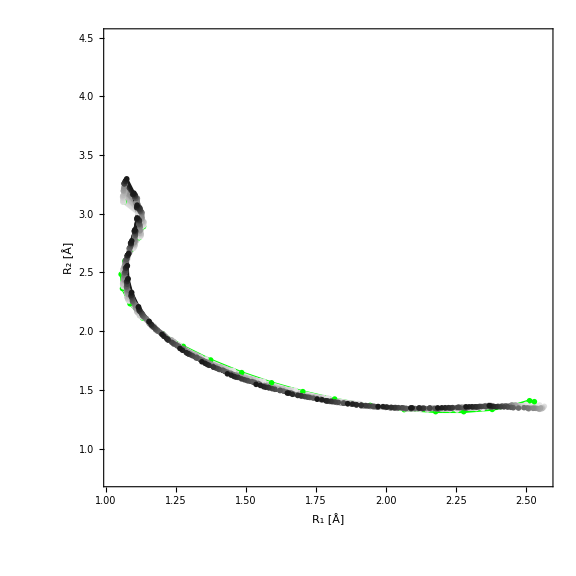

```mathematica
ListPlot[Table[String2D[i,1,2],{i,1,niter}],
Axes->False,Frame->True,ImageSize->Large,AspectRatio->1,
PlotRange->{0.75,4.5},
FrameLabel->{"R_1 [Å]","R_2 [Å]"},
Joined->True,
PlotStyle->Join[{Green},Table[GrayLevel[x],{x,0.9,0.1,-0.8/(niter-2)}],{Red}],
BaseStyle->{FontSize->16,FontFamily->"Lato",FontColor->Black},
PlotMarkers->{"OpenMarkers",Medium},
FrameStyle->Directive[Black,Thickness[0.0015]]]
```

#### The final string coordinates (from last iteration):

```mathematica
finalReq=Table[
Table[Mean[data[icoord,iwin]],{icoord,1,ncoord}],
{iwin,nwindows-nimageslast+1,nwindows}];
```

```mathematica
finalString=Table[
Table[constraint[icoord,iwin],{icoord,1,ncoord}],
{iwin,nwindows-nimageslast+1,nwindows}];
```

```mathematica
finalNewString=Table[
Table[newconstraint[icoord,iwin],{icoord,1,ncoord}],
{iwin,nwindows-nimageslast+1,nwindows}];
```

```mathematica
finalNewString2D[icoord1_,icoord2_]:=finalNewString⟦All,{icoord1,icoord2}⟧;
finalString2D[icoord1_,icoord2_]:=finalString⟦All,{icoord1,icoord2}⟧;
finalReq2D[icoord1_,icoord2_]:=finalReq⟦All,{icoord1,icoord2}⟧;
```

```mathematica
(*
coef1 and coef2 are the lists of the coefficients in linear combinations of coordinates
*)
finalNewString2Dmix[coef1_,coef2_]:=Table[
{
Sum[coef1⟦k⟧finalNewString⟦i,k⟧,{k,1,ncoord}],
Sum[coef2⟦k⟧finalNewString⟦i,k⟧,{k,1,ncoord}]
},
{i,1,Length[finalNewString]}];
finalString2Dmix[coef1_,coef2_]:=Table[
{
Sum[coef1⟦k⟧finalString⟦i,k⟧,{k,1,ncoord}],
Sum[coef2⟦k⟧finalString⟦i,k⟧,{k,1,ncoord}]
},
{i,1,Length[finalString]}];
finalReq2Dmix[coef1_,coef2_]:=Table[
{
Sum[coef1⟦k⟧finalReq⟦i,k⟧,{k,1,ncoord}],
Sum[coef2⟦k⟧finalReq⟦i,k⟧,{k,1,ncoord}]
},
{i,1,Length[finalReq]}];
```

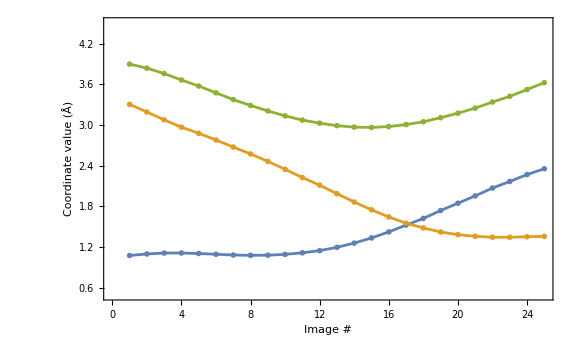

```mathematica
ListPlot[Table[finalNewString⟦All,i⟧,{i,1,ncoord}],
PlotRange->{0.5,4.5},
Axes->False,Frame->True,
Joined->True,
PlotMarkers->{"OpenMarkers",Medium},
ImageSize->Large,
BaseStyle->{FontSize->16,FontFamily->"Lato"},
FrameStyle->Directive[Black],
FrameLabel->{"Image #","Coordinate value (Å)"},
PlotLegends->Placed[{"O-H","H-S","O-S","H-OW"},{0.55,0.825}]
]
```

For example, in 2D space spanned by any two coordinates (coordinates 1 and 2, in this example):

```mathematica
s12=finalNewString2D[1,2]
Req12=finalReq2D[1,2]
```

{{1.0752,3.3037},{1.0982,3.1908},{1.1118,3.075},{1.1124,2.9671},{1.1051,2.8769},{1.0935,2.7781},{1.0829,2.6742},{1.0779,2.5725},{1.0802,2.463},{1.0921,2.3464},{1.1155,2.2243},{1.1475,2.1117},{1.196,1.9865},{1.2584,1.8644},{1.3345,1.7491},{1.4234,1.6439},{1.5239,1.5519},{1.6224,1.4826},{1.7384,1.422},{1.8461,1.3829},{1.954,1.358},{2.07,1.3453},{2.1668,1.3446},{2.2686,1.3515},{2.3542,1.3572}}

{{1.08858,3.29442},{1.09711,3.17763},{1.09961,3.06412},{1.09886,2.951},{1.09876,2.85579},{1.09722,2.78339},{1.09556,2.68611},{1.09347,2.58885},{1.0931,2.46207},{1.10341,2.35486},{1.11486,2.24245},{1.13787,2.09735},{1.17484,2.00381},{1.22872,1.87478},{1.3151,1.76123},{1.42172,1.63771},{1.53799,1.53586},{1.66125,1.46356},{1.77545,1.41694},{1.876,1.38299},{1.99093,1.35842},{2.09074,1.34504},{2.18165,1.34918},{2.27771,1.34991},{2.37663,1.35695}}

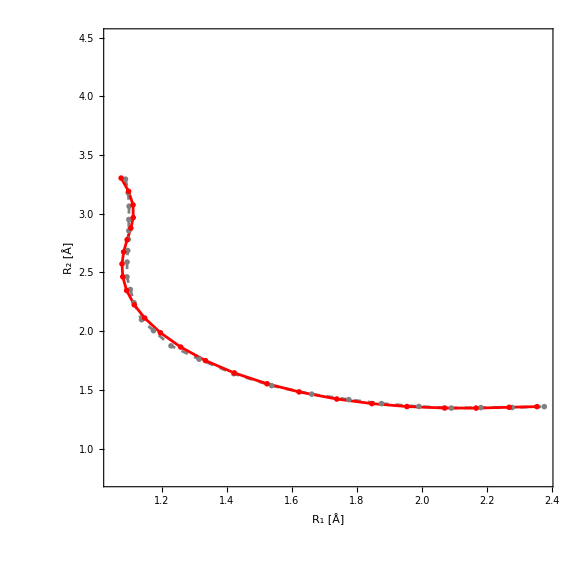

```mathematica
ListPlot[{Req12,s12},Axes->False,Frame->True,FrameLabel->{"R_1 [Å]","R_2 [Å]"},
Joined->{True,True},
PlotStyle->{{Gray,Dashed},Red},
BaseStyle->{FontSize->16,FontFamily->"Lato",FontColor->Black},
ImageSize->Large,AspectRatio->1,PlotRange->{0.75,4.5},
PlotMarkers->{"OpenMarkers",Medium},
FrameStyle->Directive[Black,Thickness[0.0015]]]
```

```mathematica
s13=finalNewString2D[1,3]
Req13=finalReq2D[1,3]
```

{{1.0752,3.8965},{1.0982,3.8373},{1.1118,3.7572},{1.1124,3.6629},{1.1051,3.5733},{1.0935,3.473},{1.0829,3.3738},{1.0779,3.2872},{1.0802,3.2064},{1.0921,3.1338},{1.1155,3.0716},{1.1475,3.0263},{1.196,2.9894},{1.2584,2.968},{1.3345,2.9633},{1.4234,2.9759},{1.5239,3.0056},{1.6224,3.0467},{1.7384,3.107},{1.8461,3.1728},{1.954,3.2475},{2.07,3.3376},{2.1668,3.4214},{2.2686,3.5212},{2.3542,3.6235}}

{{1.08858,3.89404},{1.09711,3.80981},{1.09961,3.76612},{1.09886,3.65931},{1.09876,3.55634},{1.09722,3.47412},{1.09556,3.36546},{1.09347,3.27997},{1.0931,3.22263},{1.10341,3.14532},{1.11486,3.09086},{1.13787,3.03045},{1.17484,2.99568},{1.22872,2.96594},{1.3151,2.96152},{1.42172,2.96304},{1.53799,3.00747},{1.66125,3.04664},{1.77545,3.11185},{1.876,3.1901},{1.99093,3.27455},{2.09074,3.38776},{2.18165,3.44382},{2.27771,3.54298},{2.37663,3.62614}}

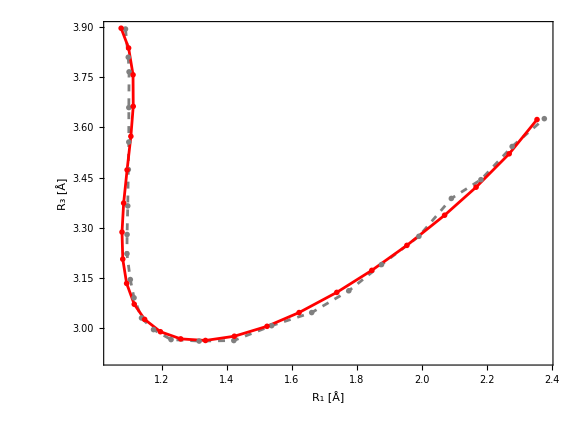

```mathematica
ListPlot[{Req13,s13},Axes->False,Frame->True,FrameLabel->{"R_1 [Å]","R_3 [Å]"},
Joined->{True,True},PlotRange->All,AspectRatio->0.75,
PlotStyle->{{Gray,Dashed},Red},
BaseStyle->{FontSize->16,FontFamily->"Lato",FontColor->Black},
ImageSize->Large,AspectRatio->1,PlotRange->{2.2,3.6},
PlotMarkers->{"OpenMarkers",Medium},
FrameStyle->Directive[Black,Thickness[0.0015]]]
```

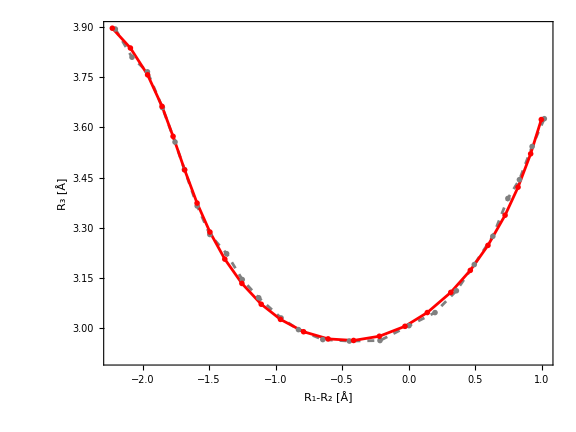

```mathematica
ListPlot[{finalReq2Dmix[{1,-1,0},{0,0,1}],finalNewString2Dmix[{1,-1,0},{0,0,1}]},
Axes->False,Frame->True,FrameLabel->{"R_1-R_2 [Å]","R_3 [Å]"},
PlotRange->All,AspectRatio->0.75,
Joined->{True,True},
PlotStyle->{{Gray,Dashed},Red},
BaseStyle->{FontSize->16,FontFamily->"Lato",FontColor->Black},
ImageSize->Large,AspectRatio->1,
PlotMarkers->{"OpenMarkers",Medium},
FrameStyle->Directive[Black,Thickness[0.0015]]]
```

#### Universal function for adding additional points (using the steps along the curve) and redistributing images

```mathematica
(* Input: *)
(* string - the list of image coordinates *)
(*          {{Subscript[x, 1],Subscript[y, 1],Subscript[z, 1],...},{Subscript[x, 2],Subscript[y, 2],Subscript[z, 2],...},...,{Subscript[x, N],Subscript[y, N],Subscript[z, N],...}}, where N is the number of images in the string; *)
(* addN - number of images to add to the string (if positives the images are added to the end of the string, if negative - to the beginning of the string); *)
(* order - order of the fitting polynomial. *)
(**)
(* Options: *)
(* Redistribute (True/False) - whether to redistribute all the images after adding the images at the end of the string (Default: False); *)
(* Linear (True/False) - whether to use a linear approximation to calculate the length of the arc along the string; if "False" then the actual line integral is evaluated numerically. *)
(* StepSize - stepsize for integration along the curve (Default: 0.0005) *)
(**)
addImages[string_,addN_,order_,OptionsPattern[{Redistribute->False,Linear->True,StepSize->0.0005,Debug->False}]]:=Module[
{debug,tail,nAdd,stepSize,tFirst,tLast,redistribute,linear,arcLength,dim,nImages,model,fit,stringPlus,stringLength,stringPlusLength,δ,δ0,dt,tprev,tlist,length,lastSegmentLength,stringFinal,fCurve,fCurveD},
redistribute=OptionValue[Redistribute];

debug=OptionValue[Debug];
linear=OptionValue[Linear];
model=Table[t^i,{i,0,order}];
dim=Length[string⟦1⟧];
nImages=Length[string];
tail=addN>0;
nAdd=Abs[addN];
stepSize=OptionValue[StepSize];

(* Polynomial Interpolation of the input string *)
fit={};
Do[
AppendTo[fit,Fit[string[[All,i]],model,t]],
{i,1,dim}];
fCurve[u_]:=fit/.{t->u};
fCurveD[u_]:=D[fit,t]/.{t->u};
arcLength[t1_,t2_]:=If[linear,Norm[fCurve[t2]-fCurve[t1]],ArcLength[fCurve[t],{t,t1,t2}]];

(* adding additional points to the input string using extrapolation *)
(* and the length of the last segment as a step along the extrapolated string *)
stringLength=ArcLength[fCurve[t],{t,1,nImages}];
If[debug,Print["Initial string length: ",stringLength]];
δ0=stringLength/(nImages-1);
If[debug,Print["Average segment length of the initial string: ",δ0]];
lastSegmentLength=If[tail,arcLength[nImages-1,nImages],arcLength[1,2]];
If[debug,Print["lastSegmentLength: ",lastSegmentLength]];
dt=If[tail,stepSize,-stepSize];
tlist={};
tprev=If[tail,nImages,1];
Monitor[
Do[
length=0;While[length<lastSegmentLength,length+=arcLength[tprev,tprev+dt];tprev+=dt];
If[debug,Print["Length during adding: ",length]];
If[tail,AppendTo[tlist,tprev],PrependTo[tlist,tprev]],
{i,1,nAdd}],
Panel@Grid[{
{"Adding ",nAdd," images: ",ProgressIndicator[i,{1,nAdd}]," Image"->i}
}]
];
If[debug,Print["Additional t-list: ",tlist]];
stringPlus=If[tail,Join[string,Table[fCurve[t],{t,tlist}]],Join[Table[fCurve[t],{t,tlist}],string]];
tFirst=If[tail,1,tlist⟦-1⟧];
tLast=If[tail,tlist⟦-1⟧,nImages+nAdd];

If[debug,Print["Total number of images after adding ",nAdd," images: ",Length[stringPlus]]];

(*Redistribute images equally along the new extended string*)
If[redistribute,
stringPlusLength=ArcLength[fCurve[t],{t,tFirst,tLast}];
If[debug,Print["Final string length: ",stringPlusLength]];
δ=stringPlusLength/(nImages+nAdd-1);
If[debug,Print["Average segment length of the final string: ",δ]];
dt=stepSize;
tlist={tFirst};
tprev=tFirst;
Monitor[
Do[
length=0;While[length<δ,length+=arcLength[tprev,tprev+dt];tprev+=dt];
If[debug,Print["Length during redistribution: ",length]];
AppendTo[tlist,tprev],
{i,1,nImages+nAdd-1}],
Panel@Grid[{
{"Redistributing ",nImages+nAdd," images: ",ProgressIndicator[i,{1,nImages+nAdd}]," Image"->i+1}
}]
];
stringFinal=Table[fCurve[t],{t,tlist}],
If[debug,Print["Final t-list: ",tlist]];
stringFinal=stringPlus
];
If[debug,Print["Number of images after redistribution: ",Length[stringFinal]]];
stringFinal
];
```

```mathematica
Length@finalString
```

25

```mathematica
finalNewStringExtended=addImages[finalNewString,2,5,Redistribute->True,Linear->False,StepSize->0.001,Debug->False];
nimageslastExtended=Length[finalNewStringExtended];
finalNewStringExtended2Dmix[coef1_,coef2_]:=Table[
{
Sum[coef1⟦k⟧finalNewStringExtended⟦i,k⟧,{k,1,ncoord}],
Sum[coef2⟦k⟧finalNewStringExtended⟦i,k⟧,{k,1,ncoord}]
},
{i,1,Length[finalNewStringExtended]}];
```

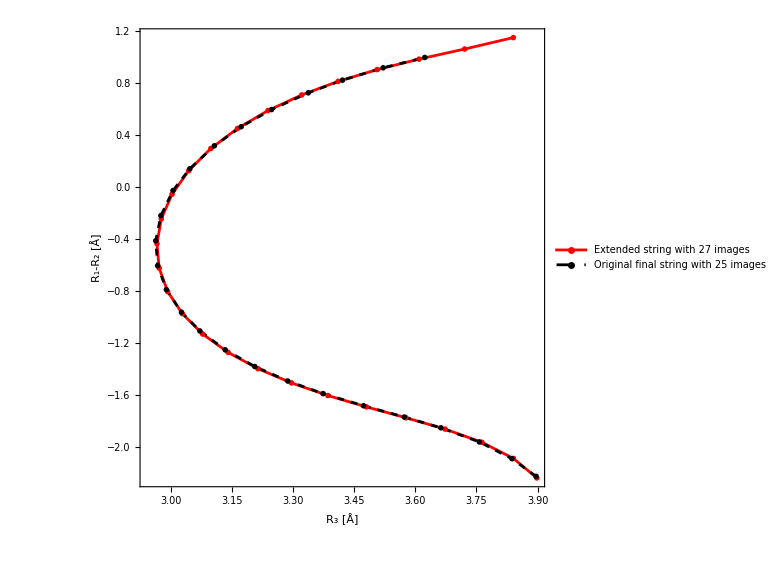

```mathematica
ListPlot[
{Reverse[finalNewStringExtended2Dmix[{1,-1,0},{0,0,1}],2],
Reverse[finalNewString2Dmix[{1,-1,0},{0,0,1}],2]},
Axes->False,Frame->True,FrameLabel->{"R_3 [Å]","R_1-R_2 [Å]"},
PlotRange->All,
Joined->{True,True},
PlotStyle->{Red,{Black,Dashed}},
ImageSize->Large,AspectRatio->1,
PlotMarkers->{"OpenMarkers",Medium},
FrameStyle->Directive[Black,Thickness[0.0015]],
LabelStyle->{18,FontFamily->"Lato"},
PlotLegends->Placed[{"Extended string with 27 images","Original final string with 25 images"},{0.65,0.5}]]
```

### Basic characteristics of the window distributions:

Mean <coordinates> in each window:

```mathematica
xmean=Table[Mean[data[icoord,iwin]],{icoord,1,ncoord},{iwin,1,nwindows}];
```

Standard deviation √(<x^2>-<x>^2) in each window:

```mathematica
σ=Table[StandardDeviation[data[icoord,iwin]],{icoord,1,ncoord},{iwin,1,nwindows}];
```

Variance <x^2>-<x>^2 in each window:

```mathematica
σ2=Table[Variance[data[icoord,iwin]],{icoord,1,ncoord},{iwin,1,nwindows}];
```

Normal window distributions (might not be a good model for bilobal distributions):

```mathematica
normal[icoord_,iwin_]:=NormalDistribution[xmean⟦icoord,iwin⟧,σ⟦icoord,iwin⟧];
```

```mathematica
Z[icoord_,iwin_,x_]:=1/(√(2π)σ⟦icoord,iwin⟧)Exp[-(x-xmean⟦icoord,iwin⟧)^2/(2σ2⟦icoord,iwin⟧)];
Zglobal[icoord_,x_]:=Sum[Z[icoord,iwin,x],{iwin,nwindows-nimageslast+1,nwindows}];
```

```mathematica
Off[General::munfl];
Manipulate[
Plot[Zglobal[icoord,x],{x,1,3.5},
PlotRange->All,Axes->False,Frame->True,
FrameLabel->{"R [Å]","PDF"},
ImageSize->Large,AspectRatio->0.75,
BaseStyle->{FontSize->18,FontFamily->"Lato",FontColor->Black},
FrameStyle->Directive[Black,Thickness[0.00175]]],
{{icoord,1,"Reaction Coordinate"},Table[k,{k,1,ncoord}]},
ControlType->Setter
]
```

### Create global grids (bins) for each coordinate

```mathematica
globalGrid={};
binwidth={};
Block[{icoord,left,right,interval,nbins,δ=0.0001,binw},
For[icoord=1,icoord<ncoord+1,icoord++,
left=Min[Flatten@Join[Table[data[icoord,iwin],{iwin,1,nwindows}]]]-δ;
right=Max[Flatten@Join[Table[data[icoord,iwin],{iwin,1,nwindows}]]]+δ;
interval=right-left;
binw=interval/numbins;
AppendTo[binwidth,binw];
AppendTo[globalGrid,Table[left+k*binw,{k,0,numbins}]]
]
];
```

Binwidths for each coordinate:

```mathematica
binwidth
```

{0.08293,0.108145,0.055295}

### Unnormalized biased 1D histograms h_i^(b)(R_k) and normalized biased 1D distribution functions ρ_i^(b)(R_k): (iwin - window; icoord - reaction coordinate; please be patient, takes some time to evaluate)

```mathematica
Do[
hb[icoord,iwin]=Block[{i,hist,grid,bars,bins},
hist=HistogramList[data[icoord,iwin],{globalGrid⟦icoord⟧},"Count"];
grid=hist⟦1⟧;
bars=hist⟦2⟧;
bins={};
For[i=1,i<Length[grid],i++,AppendTo[bins,(grid⟦i⟧+grid⟦i+1⟧)/2]];
Table[{bins⟦k⟧,bars⟦k⟧},{k,1,Length[bars]}]
],
{icoord,1,ncoord},{iwin,1,nwindows}];
Do[
ρb[icoord,iwin]=Block[{i,hist,grid,bars,bins},
hist=HistogramList[data[icoord,iwin],{globalGrid⟦icoord⟧},"Probability"];
grid=hist⟦1⟧;
bars=hist⟦2⟧;
bins={};
For[i=1,i<Length[grid],i++,AppendTo[bins,(grid⟦i⟧+grid⟦i+1⟧)/2]];
Table[{bins⟦k⟧,bars⟦k⟧},{k,1,Length[bars]}]
],
{icoord,1,ncoord},{iwin,1,nwindows}];//EchoTiming
```

5.67745

Just to see how the bias distribution functions look like:

```mathematica
Manipulate[
ListPlot[hb[icoord,iwin],
PlotRange->{{1,4},All},
Joined->True,
PlotRange->All,Axes->False,Frame->True,
FrameLabel->{"R [Å]","h^(biased)(R)"},
ImageSize->Large,AspectRatio->0.75,
BaseStyle->{FontSize->18,FontFamily->"Lato",FontColor->Black},
FrameStyle->Directive[Black,Thickness[0.00175]],
PlotMarkers->Automatic,
PlotLabel->Style["Window "<>ToString[iwin]<>" for reaction coordinate "<>ToString[icoord],Red,18]
],
{{iwin,1,"Window"},1,nwindows,1},
{{icoord,1,"Reaction Coordinate"},Table[k,{k,1,ncoord}]},
ControlType->{Automatic,Setter}
]
```

```mathematica
Manipulate[
ListPlot[ρb[icoord,iwin],
PlotRange->{{1,4},{-0.01,1.01}},
Joined->True,
PlotRange->All,Axes->False,Frame->True,
FrameLabel->{"R [Å]","ρ^(biased)(R)"},
ImageSize->Large,AspectRatio->0.75,
BaseStyle->{FontSize->18,FontFamily->"Lato",FontColor->Black},
FrameStyle->Directive[Black,Thickness[0.00175]],
PlotMarkers->Automatic,
PlotLabel->Style["Window "<>ToString[iwin]<>" for reaction coordinate "<>ToString[icoord],Red,18]
],
{{iwin,1,"Window"},1,nwindows,1},
{{icoord,1,"Reaction Coordinate"},Table[k,{k,1,ncoord}]},
ControlType->{Automatic,Setter}
]
```

## WHAM for PMF(x_1,x_2,...,x_ncoord) and projected PMFs

### Calculate biasing potential at the sampled points for all windows (takes some time, check the weather for tomorrow and maybe have a cup of tea/coffee)

```mathematica
nwindows
```

750

```mathematica
Monitor[
Wlist=Table[
Sum[1/2 force[icoord,iwin]*(data[icoord,jwin]⟦k⟧-constraint[icoord,iwin])^2,{icoord,1,ncoord}],
{iwin,1,nwindows},
{jwin,1,nwindows},
{k,1,nsamples⟦jwin⟧}],
Panel@Grid[{
{ProgressIndicator[Dynamic[iwin],{1,nwindows}],"Window i:"->iwin},
{ProgressIndicator[Dynamic[jwin],{1,nwindows}],"Window j:"->jwin}
},Alignment->{{Right,Left},{Bottom,Bottom,Bottom}},Spacings->{1,0.5}]
];//EchoTiming
```

585.768

```mathematica
expWlist=SetPrecision[Chop[N@Quiet@Exp[-β Wlist]],$MachinePrecision];//EchoTiming
Speak["Calculation of biasing potential lists is finished"];
```

64.1347

```mathematica
MinMax[expWlist]
```

{0,0.999993290428729}

### Self-consistent solution of equations for the free energy constants f_i (for full multi-dimensional PMF, binless method) (-- may take a really long time depending on the desired tolerance, go have a lunch/dinner --) (-- If you’ve done it already skip this cell and go to the next to read constants from disk --)

#### Monitored version:

```mathematica
nwindows
```

750

```mathematica
f0=ConstantArray[0,nwindows];
Monitor[
Block[
{error=99.9,tolerance=0.001,
maxiter=20000,iter=0,
time=0,totaltime=0,timeperiteration=0,
fprev=f0,fexp,fexpprev,fexpfact,
iwin,lconf,jwin,
denominator,expW
},
fexpprev=Exp[β fprev];
fexpfact=nsamples*fexpprev;
Speak["Starting WHAM iterations."];
While[error>tolerance&&iter<maxiter,
time=TimeUsed[];
iter+=1;
fexp=ConstantArray[0,nwindows];
For[iwin=1,iwin<nwindows+1,iwin++,
For[lconf=1,lconf<nsamples⟦iwin⟧+1,lconf++,
expW=expWlist⟦All,iwin,lconf⟧;
denominator=Dot[expW,fexpfact];
If[Abs@denominator<$MachineEpsilon,Print["Window: ",iwin," Sample: ",lconf," → denominator is ",denominator]];
fexp+=expW/denominator
]
];
f=-1/β Log[fexp];
f=f-f⟦1⟧;
error=Max[Abs[f-fprev]];
fprev=f;
fexpprev=Exp[β fprev];
fexpfact=nsamples*fexpprev;
timeperiteration=TimeUsed[]-time;
totaltime+=timeperiteration
];
If[iter<maxiter,
Speak["Converged after "<>ToString[iter]<> " iterations"],
Speak["Failed to converge after "<>ToString[maxiter]<> " iterations"]
];
WriteString["stdout","\n"];
Print["After ",iter," iterations the max absolute error is ",error," (tolerance is ",tolerance,")"];
Print["Total time used: ",totaltime," (average time per iteration: ",totaltime/iter,")"];
],
Panel[
"Iteration: "<>IntegerString[iter,10,5]<>" ==>    Max absolute error: "<>ToString[PaddedForm[error,{8,6}]]<>";    Time used so far: "<>ToString[PaddedForm[totaltime,{10,3}]]<>";    Time per iteration: "<>ToString[PaddedForm[timeperiteration,{8,3}]]
]
];
Export["fconstants.dat",f,"Data"];
file=OpenWrite["fconstants-list.dat"];
Write[file,f];
Close[file];
Print["Free energy constants are damped to disk and stored in fconstants.dat and fconstant-list.dat files"]
```

After 2902 iterations the max absolute error is 0.00099946 (tolerance is 0.001)

Total time used: 43096.5 (average time per iteration: 14.8506)

Free energy constants are damped to disk and stored in fconstants.dat and fconstant-list.dat files

Read f-constants from disk file
(evaluate the following cell and then click on a button of your choice):

```mathematica
Button[Mouseover[Style["Read free energy constants from disk",Red],Style["Read free energy constants from disk",Darker@Green]],
file=OpenRead["fconstants-list.dat"];
fcopy=Read[file];
Close[file];
f=fcopy;
Print["Free energy constants are read from disk and stored in fcopy"]
]
```

Visualize the free energy constants:

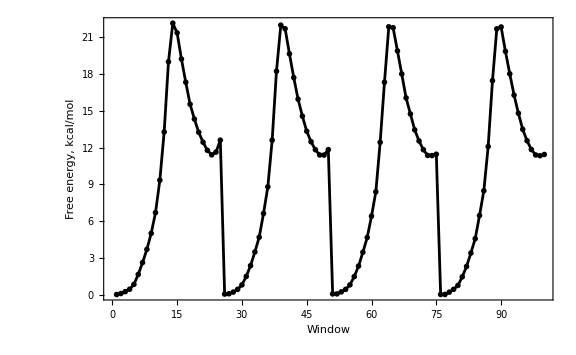

```mathematica
ListPlot[f⟦1;;100⟧,
BaseStyle->{18,FontFamily->"Lato"},
Joined->True,
FrameLabel->{"Window","Free energy,  kcal/mol"},
PlotStyle->Black,
PlotMarkers->{"OpenMarkers",Medium},
ImageSize->Large,Axes->False,Frame->True,
FrameStyle->Directive[Black,Thick]
]
```

## Weighted data in each window (for unbiased distributions)

```mathematica
Length[f]
```

750

```mathematica
tmprweights=Flatten@Table[
(nsamples*Exp[β f]) . expWlist⟦All,iwin,k⟧,
{iwin,1,nwindows,1},
{k,1,nsamples[[iwin]],1}
];//EchoTiming
```

9.72978

```mathematica
$MachineEpsilon
```

2.22045×10^-16

```mathematica
Select[tmprweights,#<$MachineEpsilon&]
```

{}

```mathematica
$MachineEpsilon
```

2.22045×10^-16

```mathematica
WHAMweights={};
Monitor[
Block[{expW, expf,expffactor={},denominator,iwin,k,weightsi},
expf=Exp[β f];
expffactor=nsamples*expf;
For[iwin=1,iwin<nwindows+1,iwin++,
weightsi={};
For[k=1,k<nsamples⟦iwin⟧+1,k++,
expW=expWlist⟦All,iwin,k⟧;
denominator=Chop@N[expW . expffactor];
AppendTo[weightsi,If[denominator>$MachineEpsilon,1/denominator,0]]
];
AppendTo[WHAMweights,weightsi]
]
],
Panel@Grid[{
{"Window",ProgressIndicator[iwin,{1,nwindows}],iwin,"Sample:",k," weight: ",1/denominator}
},Alignment->{{Right,Left,Center,Right,Left}},Spacings->1]
];
```

Now, weight all the data in all windows:

```mathematica
Monitor[
Do[
weighteddata[icoord,iwin]=WeightedData[data[icoord,iwin],WHAMweights⟦iwin⟧],
{icoord,1,ncoord},
{iwin,1,nwindows}
],
Panel@Grid[{
{ProgressIndicator[iwin,{1,nwindows}],"\twindow\t"->iwin},
{ProgressIndicator[icoord,{1,ncoord}],"\tcoordinate\t"->icoord}
},Alignment->{{Right,Left},{Bottom,Bottom,Bottom}},Spacings->{1,0.5}]
];
```

Now, weight multidimensional data in all windows (might be very large nested lists):

```mathematica
Print["Memory used so far (GB): ",MemoryInUse[]/1024./1024./1024.];
```

Memory used so far (GB): 2.77875

```mathematica
memBefore=MemoryInUse[];
weighteddataAll=WeightedData[dataAll,Flatten@WHAMweights];
memAfter=MemoryInUse[];
Print["The list with weighted multidimensional sampling data used ",(memAfter-memBefore)/1024./1024.," MegaBytes"];
```

The list with weighted multidimensional sampling data used 2.29055 MegaBytes

## Projected 1D and 2D unbiased distributions

### One-dimensional unbiased (unnormalized) distributions

```mathematica
Monitor[
Do[
ρ1Dwin[icoord,iwin]=Block[{i,hist,grid,bars,bins},
hist=HistogramList[weighteddata[icoord,iwin],{globalGrid⟦icoord⟧}];
grid=hist⟦1⟧;
bars=hist⟦2⟧;
bins={};
For[i=1,i<Length[grid],i++,AppendTo[bins,(grid⟦i⟧+grid⟦i+1⟧)/2]];
Table[{bins⟦k⟧,bars⟦k⟧},{k,1,Length[bars]}]
],
{icoord,1,ncoord},{iwin,1,nwindows}
],
Panel@Grid[{
{"Coordinate",ProgressIndicator[icoord,{1,ncoord}],icoord},
{"Window",ProgressIndicator[iwin,{1,nwindows}],iwin}
},Alignment->{{Right,Left}},Spacings->{1,1}]
];
```

```mathematica
Manipulate[ListLinePlot[ρ1Dwin[icoord,iwin],ImageSize->Large,PlotRange->All,PlotMarkers->{"OpenMarkers",Small}],
{{icoord,1,"Reaction Coordinate"},Table[k,{k,1,ncoord}]},
{iwin,1,nwindows,1},
FrameLabel->{None,None,"Unbiased PDFs for each coordinate in each window"},LabelStyle->{FontSize->12}]
```

### (unbiased) Averaged values of reaction coordinates in each window

```mathematica
Monitor[
Do[
RCwin[icoord,iwin]=Mean[weighteddata[icoord,iwin]];
RCBwin[icoord,iwin]=Mean[data[icoord,iwin]],
{icoord,1,ncoord},{iwin,1,nwindows}
],
Panel@Grid[{
{"Coordinate",ProgressIndicator[icoord,{1,ncoord}],icoord},
{"Window",ProgressIndicator[iwin,{1,nwindows}],iwin}
},Alignment->{{Right,Left}},Spacings->{1,1}]
];
```

```mathematica
Manipulate[
ListLinePlot[
{Table[RCBwin[icoord,iwin],{iwin,nwindows-nimageslast+1,nwindows}],
Table[RCwin[icoord,jwin],{jwin,nwindows-nimageslast+1,nwindows}]},
BaseStyle->{16,FontFamily->"Lato"},LabelStyle->{16,FontFamily->"Lato"},
ImageSize->Large,PlotLegends->{"Biased","Unbiased"},PlotStyle->{Dashed,Red},
Axes->False,Frame->True,FrameLabel->{"Images","Coordinate Value (Å)"},PlotMarkers->{"OpenMarkers",Medium}],
{{icoord,1,"Reaction Coordinate"},Table[k,{k,1,ncoord}]},
ControlType->Setter,
FrameLabel->{None,None,"Unbiased Averages for Each Image of the Last Iteration\ncalculated with global WHAM weights"},LabelStyle->{Red,FontSize->12}]
```

### (truly unbiased) Averaged values of reaction coordinates in each window: (⟨R exp[β w]⟩_b)/(⟨exp[β w]⟩_b)

```mathematica
minWlist=Table[Min[Wlist⟦iwin,iwin,All⟧],{iwin,1,nwindows}];//EchoTiming
```

6.0828

```mathematica
Wlist0=Table[Wlist⟦iwin,iwin,All⟧-minWlist⟦iwin⟧,{iwin,1,nwindows}];
expPWlist0=Exp[β Wlist0];
```

```mathematica
Monitor[
Do[
RCUwin[icoord,iwin]=
Mean[data[icoord,iwin]*expPWlist0⟦iwin⟧]/Mean[expPWlist0⟦iwin⟧],
{icoord,1,ncoord},{iwin,1,nwindows}
],
Panel@Grid[{
{"Coordinate",ProgressIndicator[icoord,{1,ncoord}],icoord},
{"Window",ProgressIndicator[iwin,{1,nwindows}],iwin}
},Alignment->{{Right,Left}},Spacings->{1,1}]
];
```

```mathematica
ncoord
```

3

```mathematica
Manipulate[
ListLinePlot[Table[RCUwin[icoord,iwin],{iwin,nwindows-nimageslast+1,nwindows}],
BaseStyle->{16,FontFamily->"Lato"},LabelStyle->{16,FontFamily->"Lato"},
PlotRange->All,ImageSize->Large,Axes->False,Frame->True,FrameLabel->{"Images","Coordinate Value (Å)"},PlotMarkers->{"OpenMarkers",Medium}],
{{icoord,1,"Reaction Coordinate"},Table[k,{k,1,ncoord}]},
ControlType->Setter,
FrameLabel->{None,None,Style["Unbiased Averages for Each Image of the Last Iteration\ncalculated for each window separately",FontFamily->"Lato",16,Red]}]
```

```mathematica
Manipulate[
ListLinePlot[
{Table[RCBwin[icoord,iwin],{iwin,nwindows-nimageslast+1,nwindows}],
Table[RCwin[icoord,jwin],{jwin,nwindows-nimageslast+1,nwindows}],
Table[RCUwin[icoord,iwin],{iwin,nwindows-nimageslast+1,nwindows}]},
BaseStyle->{16,FontFamily->"Lato"},LabelStyle->{16,FontFamily->"Lato"},
ImageSize->Large,PlotLegends->{"Biased","Unbiased","(truly) unbiased"},PlotStyle->{Dashed,{Dashed,Red},Red},
Axes->False,Frame->True,FrameLabel->{"Images","Coordinate Value (Å)"},PlotMarkers->{"OpenMarkers",Medium}],
{{icoord,1,"Reaction Coordinate"},Table[k,{k,1,ncoord}]},
ControlType->Setter,
FrameLabel->{None,None,"Unbiased Averages for Each Image of the Last Iteration\ncalculated with global WHAM weights"},LabelStyle->{Red,FontSize->16}]
```

### Projected One-dimensional PMFs

```mathematica
Do[
Block[{bins,bars,Fmin,minCount},
minCount=0;
bins=ρ1Dwin[icoord,1]⟦All,1⟧;
bars=Sum[ρ1Dwin[icoord,iwin]⟦All,2⟧,{iwin,1,nwindows}];
ρ1D[icoord]=Table[{bins⟦k⟧,bars⟦k⟧},{k,1,Length[bars]}];
Fmin=Min[-1/β Log[Select[bars,#>minCount&]]];
F1D[icoord]=Table[{bins⟦k⟧,-1/β Log[If[bars⟦k⟧>0,bars⟦k⟧,1]]-Fmin},{k,1,Length[bars]}]
],
{icoord,1,ncoord}
];
```

Let’s visualize projected 1D PMFs

```mathematica
Manipulate[
GraphicsRow[
{ListPlot[ρ1D[icoord],
BaseStyle->{12,FontFamily->"Lato"},LabelStyle->{12,FontFamily->"Lato"},
PlotRange->All,Axes->False,Frame->True,ImageSize->Large,
Joined->True,PlotMarkers->{"OpenMarkers",Small},
FrameLabel->{"R, Å","PDF"},PlotLabel->"Coordinate "<>ToString[icoord]],
ListPlot[F1D[icoord],
BaseStyle->{12,FontFamily->"Lato"},LabelStyle->{12,FontFamily->"Lato"},
PlotRange->All,Axes->False,Frame->True,ImageSize->Large,
Joined->True,PlotMarkers->{"OpenMarkers",Small},
PlotStyle->Blue,
FrameLabel->{"R, Å","PMF, kcal/mol"},PlotLabel->"Coordinate "<>ToString[icoord]]}
],
{{icoord,1,"Reaction Coordinate"},Table[k,{k,1,ncoord}]},
ControlType->Setter
]
```

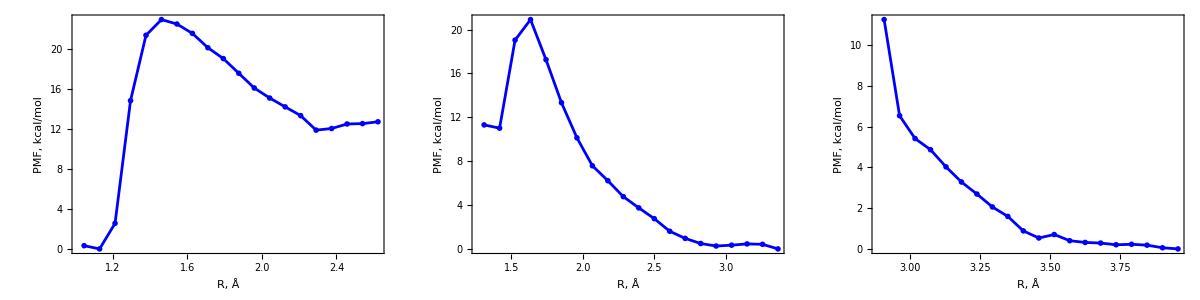

```mathematica
Grid[{
Table[ListPlot[{F1D[i]},
PlotRange->All,ImageSize->Medium,Axes->False,Frame->True,
BaseStyle->{16,FontFamily->"Lato"},LabelStyle->{16,FontFamily->"Lato"},
Joined->True,PlotMarkers->{"OpenMarkers",Small},
PlotStyle->{Blue},
FrameLabel->{{"PMF, kcal/mol",None},{"R, Å","Coordinate "<>ToString[i]}}],
{i,1,ncoord}]
},
Spacings->2
]
```

### One-dimensional unbiased (unnormalized) distributions for linear combinations of coordinates

coef is a list of coefficients (of length ncoord) defining a linear combination of coordinates

First, global grids:

```mathematica
gGridmix[coef_]:=Module[{interval,left,right,nbins,δ=0.001,binw},
left=Min[Flatten@Join[Table[Sum[coef⟦icoord⟧data[icoord,iwin],{icoord,1,ncoord}],{iwin,1,nwindows}]]]-δ;
right=Max[Flatten@Join[Table[Sum[coef⟦icoord⟧data[icoord,iwin],{icoord,1,ncoord}],{iwin,1,nwindows}]]]+δ;
interval=right-left;
binw=interval/numbins;
(*nbins=Ceiling[interval/binwidth];*)
Table[left+k*binw,{k,0,numbins}]
];
```

```mathematica
ρ1Dmixwin[iwin_,coef_]:=Module[{mdata,wdata,grid,left,right,interval,nbins,hist,bars,bins,i},
mdata=Sum[coef⟦icoord⟧data[icoord,iwin],{icoord,1,ncoord}];
wdata=WeightedData[mdata,WHAMweights⟦iwin⟧];
hist=HistogramList[wdata,{gGridmix[coef]}];
grid=hist⟦1⟧;
bars=hist⟦2⟧;
bins={};
For[i=1,i<Length[grid],i++,AppendTo[bins,(grid⟦i⟧+grid⟦i+1⟧)/2]];
Table[{bins⟦k⟧,bars⟦k⟧},{k,1,Length[bars]}]
];
```

```mathematica
ρ1Dmix[coef_]:=Module[{bins,bars},
bins=ρ1Dmixwin[1,coef]⟦All,1⟧;
bars=Sum[ρ1Dmixwin[iwin,coef]⟦All,2⟧,{iwin,1,nwindows}];
Table[{bins⟦k⟧,bars⟦k⟧},{k,1,Length[bars]}]
];
F1Dmix[coef_,OptionsPattern[{MinCount->0}]]:=Module[{bins,bars,Fmin,minCount},
minCount=OptionValue[MinCount];
bins=ρ1Dmixwin[1,coef]⟦All,1⟧;
bars=Sum[ρ1Dmixwin[iwin,coef]⟦All,2⟧,{iwin,1,nwindows}];
Fmin=Min[-1/β Log[Select[bars,#>minCount&]]];
Table[{bins⟦k⟧,-1/β Log[If[bars⟦k⟧>0,bars⟦k⟧,1]]-Fmin},{k,1,Length[bars]}]
];
```

For example,

```mathematica
F12=F1Dmix[{1,-1,0}];//EchoTiming
ρ12=ρ1Dmix[{1,-1,0}];//EchoTiming
```

85.361

86.8787

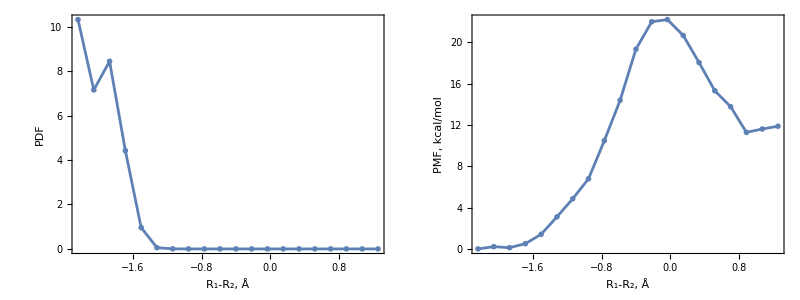

```mathematica
Grid[{
{ListLinePlot[ρ12,ImageSize->Large,PlotRange->All,Axes->False,BaseStyle->{16},Frame->True,FrameLabel->{"R_1-R_2, Å","PDF"},PlotMarkers->{"OpenMarkers",Small}],
ListLinePlot[F12,ImageSize->Large,PlotRange->All,Axes->False,BaseStyle->{16},Frame->True,FrameLabel->{"R_1-R_2, Å","PMF, kcal/mol"},PlotMarkers->{"OpenMarkers",Small}]}
},Spacings->2]
```

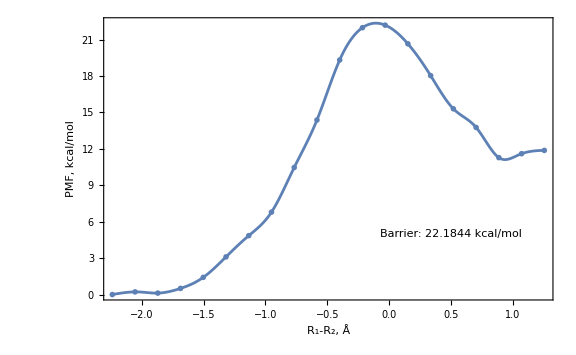

```mathematica
ListLinePlot[F12,
PlotRange->All,Axes->False,Frame->True,
InterpolationOrder->3,
ImageSize->Large,
BaseStyle->{FontFamily->"Lato",16},
FrameStyle->Directive[Black,16],
LabelStyle->Directive[Black,FontSize->16],
FrameLabel->{"R_1-R_2, Å","PMF, kcal/mol"},
PlotMarkers->{"OpenMarkers",Medium},
Epilog->Text["Barrier: "<>ToString[Max[F12⟦All,2⟧]-Min[F12⟦All,2⟧⟦1;;7⟧]]<>" kcal/mol",{0.5,5.0}]
]
```

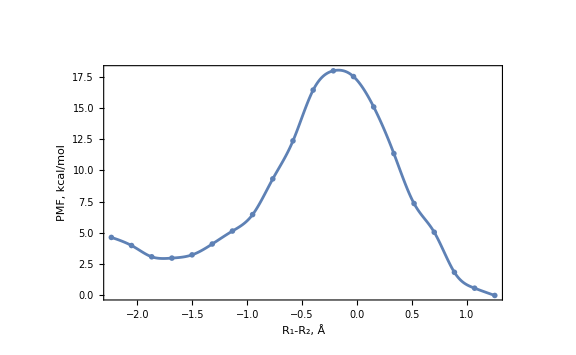

### Two-dimensional unbiased (unnormalized) distributions

```mathematica
ρ2Dwin[iwin_,icoord1_,icoord2_]:=Module[{data2D,wdata2D,hist2D,grid2D,bars2D,bins1,bins2,nbins1,nbins2},
data2D=Table[{data[icoord1,iwin]⟦k⟧,data[icoord2,iwin]⟦k⟧},{k,1,nsamples⟦iwin⟧}];
wdata2D=WeightedData[data2D,WHAMweights⟦iwin⟧];
hist2D=HistogramList[wdata2D,{{globalGrid⟦icoord1⟧},{globalGrid⟦icoord2⟧}}];
grid2D=hist2D⟦1⟧;
bars2D=hist2D⟦2⟧;
nbins1=Length@grid2D⟦1⟧;
nbins2=Length@grid2D⟦2⟧;
bins1={};
bins2={};
Do[AppendTo[bins1,(grid2D⟦1,i⟧+grid2D⟦1,i+1⟧)/2],{i,1,nbins1-1}];
Do[AppendTo[bins2,(grid2D⟦2,i⟧+grid2D⟦2,i+1⟧)/2],{i,1,nbins2-1}];
Flatten[Table[{bins1⟦i⟧,bins2⟦j⟧,bars2D⟦i,j⟧},{j,1,nbins2-1},{i,1,nbins1-1}],1]
];
```

```mathematica
ρ2D[icoord1_,icoord2_]:=Module[{ρ1,bins1,bins2,bars},
ρ1=ρ2Dwin[1,icoord1,icoord2];
bins1=ρ1⟦All,1⟧;
bins2=ρ1⟦All,2⟧;
bars=Sum[ρ2Dwin[iwin,icoord1,icoord2]⟦All,3⟧,{iwin,1,nwindows}];
Table[{bins1⟦k⟧,bins2⟦k⟧,bars⟦k⟧},{k,1,Length[bars]}]
];
```

```mathematica
F2D[icoord1_,icoord2_]:=Module[{ρ1,bins1,bins2,bars,Fmin},
ρ1=ρ2Dwin[1,icoord1,icoord2];
bins1=ρ1⟦All,1⟧;
bins2=ρ1⟦All,2⟧;
bars=Sum[ρ2Dwin[iwin,icoord1,icoord2]⟦All,3⟧,{iwin,1,nwindows}];
Fmin=Min[-1/β Log[Select[bars,#>0&]]];
Table[{bins1⟦k⟧,bins2⟦k⟧,-1/β Log[bars⟦k⟧]-Fmin},{k,1,Length[bars]}]
];
```

For example,

```mathematica
F2D12=F2D[1,2]/.{Indeterminate->999.999};//EchoTiming
```

5.77088

And contour plot (with strings superimposed):

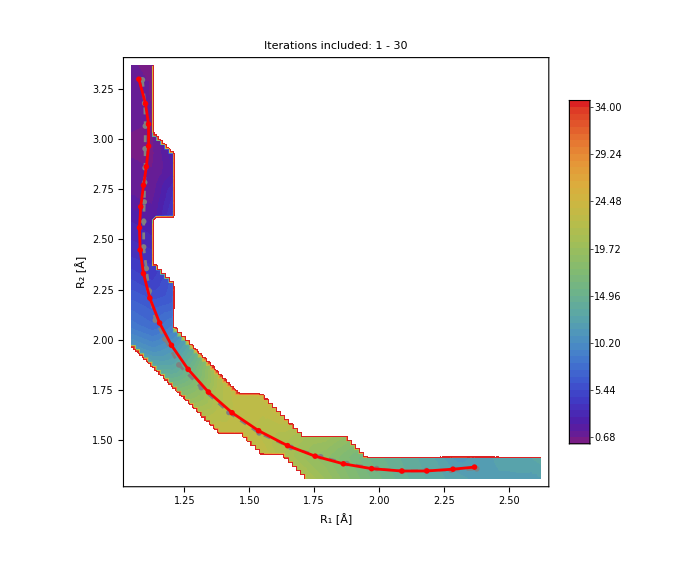

```mathematica
Show[
ListContourPlot[F2D12,
PlotLabel->"Iterations included: "<>ToString[iterationsSelected⟦1⟧]<>" - "<>ToString[iterationsSelected⟦-1⟧]<>"\n",
PlotRange->{0,35},
ContourStyle->None,
Contours->50,
ContourShading->Automatic,
PerformanceGoal->"Quality",
MaxPlotPoints->100,
ColorFunction->"Rainbow",
ClippingStyle->None,
InterpolationOrder->3,
PlotLegends->Automatic,
LabelStyle->Directive[Black,16],
ImageSize->Large,
FrameStyle->Directive[Black,Thickness[0.0015]],
BaseStyle->{FontSize->16,FontFamily->"Lato"},
FrameLabel->{"R_1 [Å]","R_2 [Å]" }
],
ListPlot[finalReq2D[1,2],PlotStyle->{Dashed,Gray},Joined->True,PlotMarkers->{"OpenMarkers",Medium}],
ListPlot[finalString2D[1,2],Joined->True,PlotStyle->Red,PlotMarkers->{"OpenMarkers",Medium}]
]
```

### Two-dimensional biased (unnormalized) distributions for linear combinations of coordinates

```mathematica
ρbiased2Dmixwin[iwin_,coef1_,coef2_]:=Module[{data2D,wdata2D,hist2D,grid2D,bars2D,bins1,bins2,nbins1,nbins2},
data2D=Table[{Sum[coef1⟦icoord⟧data[icoord,iwin],{icoord,1,ncoord}]⟦k⟧,Sum[coef2⟦icoord⟧data[icoord,iwin],{icoord,1,ncoord}]⟦k⟧},{k,1,nsamples⟦iwin⟧}];
hist2D=HistogramList[data2D,{{gGridmix[coef1]},{gGridmix[coef2]}}];
grid2D=hist2D⟦1⟧;
bars2D=hist2D⟦2⟧;
nbins1=Length@grid2D⟦1⟧;
nbins2=Length@grid2D⟦2⟧;
bins1={};
bins2={};
Do[AppendTo[bins1,(grid2D⟦1,i⟧+grid2D⟦1,i+1⟧)/2],{i,1,nbins1-1}];
Do[AppendTo[bins2,(grid2D⟦2,i⟧+grid2D⟦2,i+1⟧)/2],{i,1,nbins2-1}];
Flatten[Table[{bins1⟦i⟧,bins2⟦j⟧,bars2D⟦i,j⟧},{j,1,nbins2-1},{i,1,nbins1-1}],1]
];
```

```mathematica
ρbiased2Dmix[coef1_,coef2_]:=Module[{ρ1,bins1,bins2,bars},
ρ1=ρbiased2Dmixwin[1,coef1,coef2];
bins1=ρ1⟦All,1⟧;
bins2=ρ1⟦All,2⟧;
bars=Sum[ρbiased2Dmixwin[iwin,coef1,coef2]⟦All,3⟧,{iwin,1,nwindows}];
Table[{bins1⟦k⟧,bins2⟦k⟧,bars⟦k⟧},{k,1,Length[bars]}]
];
```

```mathematica
Fbiased2Dmix[coef1_,coef2_]:=Module[{ρ1,bins1,bins2,bars,Fmin},
ρ1=ρbiased2Dmixwin[1,coef1,coef2];
bins1=ρ1⟦All,1⟧;
bins2=ρ1⟦All,2⟧;
bars=Sum[ρbiased2Dmixwin[iwin,coef1,coef2]⟦All,3⟧,{iwin,1,nwindows}];
Fmin=Min[-1/β Log[Select[bars,#>0&]]];
Table[{bins1⟦k⟧,bins2⟦k⟧,-1/β Log[bars⟦k⟧]-Fmin},{k,1,Length[bars]}]
];
```

For example (takes some time, maybe 3-5 minutes, be patient)

```mathematica
ρbiased2Dr12r3=ρbiased2Dmix[{1,-1,0},{0,0,1}];//EchoTiming
```

177.095

```mathematica
Max[ρbiased2Dr12r3⟦All,3⟧]
```

1844

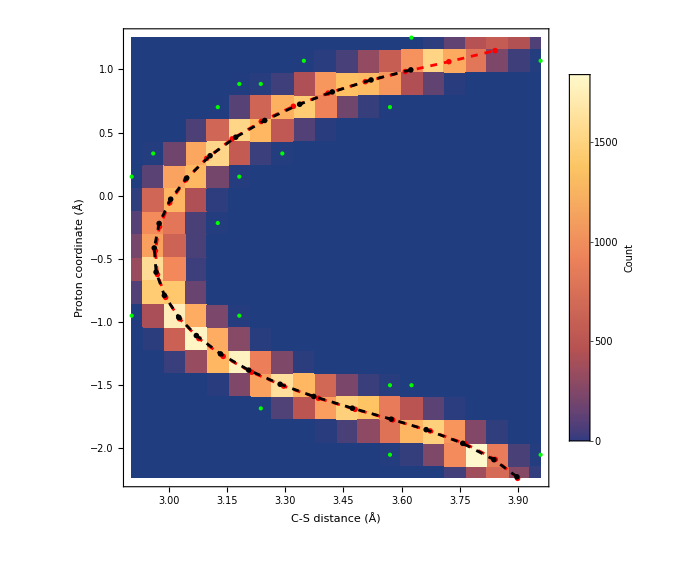

```mathematica
ρbiased2Dr12r3Jiayun=Table[{ρbiased2Dr12r3⟦i,2⟧,ρbiased2Dr12r3⟦i,1⟧,ρbiased2Dr12r3⟦i,3⟧},{i,1,Length[ρbiased2Dr12r3]}];
finalNewString2DmixJiayun=Reverse[finalNewString2Dmix[{1,-1,0},{0,0,1}],2];
finalNewStringExtended2DmixJiayun=Reverse[finalNewStringExtended2Dmix[{1,-1,0},{0,0,1}],2];
lowCountBins=Select[ρbiased2Dr12r3Jiayun,0<#⟦3⟧<10&]⟦All,{1,2}⟧;
Show[
ListDensityPlot[ρbiased2Dr12r3Jiayun,
Mesh->None,InterpolationOrder->0,PlotRange->{1,2700},
ImageSize->Large,
FrameStyle->Directive[Black,Thickness[0.003]],
BaseStyle->{FontSize->20,FontFamily->"Lato"},FrameLabel->{"C-S distance (Å)","Proton coordinate (Å)" },
PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{10,0},LegendLabel->"Count",LabelStyle->{FontFamily->"Lato",18},LegendMarkerSize->500],Right],
ClippingStyle->White,
Epilog->{Green,PointSize->Large,Point[lowCountBins]}
],
ListPlot[finalNewStringExtended2DmixJiayun,Joined->True,PlotMarkers->{"OpenMarkers",Medium},PlotStyle->{Red,Dashed}],
ListPlot[finalNewString2DmixJiayun,Joined->True,PlotMarkers->{"OpenMarkers",Medium},PlotStyle->{Black,Dashed}]
]
```

### Two-dimensional unbiased (unnormalized) distributions for linear combinations of coordinates

```mathematica
ρ2Dmixwin[iwin_,coef1_,coef2_]:=Module[{data2D,wdata2D,hist2D,grid2D,bars2D,bins1,bins2,nbins1,nbins2},
data2D=Table[{Sum[coef1⟦icoord⟧data[icoord,iwin],{icoord,1,ncoord}]⟦k⟧,Sum[coef2⟦icoord⟧data[icoord,iwin],{icoord,1,ncoord}]⟦k⟧},{k,1,nsamples⟦iwin⟧}];
wdata2D=WeightedData[data2D,WHAMweights⟦iwin⟧];
hist2D=HistogramList[wdata2D,{{gGridmix[coef1]},{gGridmix[coef2]}}];
grid2D=hist2D⟦1⟧;
bars2D=hist2D⟦2⟧;
nbins1=Length@grid2D⟦1⟧;
nbins2=Length@grid2D⟦2⟧;
bins1={};
bins2={};
Do[AppendTo[bins1,(grid2D⟦1,i⟧+grid2D⟦1,i+1⟧)/2],{i,1,nbins1-1}];
Do[AppendTo[bins2,(grid2D⟦2,i⟧+grid2D⟦2,i+1⟧)/2],{i,1,nbins2-1}];
Flatten[Table[{bins1⟦i⟧,bins2⟦j⟧,bars2D⟦i,j⟧},{j,1,nbins2-1},{i,1,nbins1-1}],1]
];
```

```mathematica
ρ2Dmix[coef1_,coef2_]:=Module[{ρ1,bins1,bins2,bars},
ρ1=ρ2Dmixwin[1,coef1,coef2];
bins1=ρ1⟦All,1⟧;
bins2=ρ1⟦All,2⟧;
bars=Sum[ρ2Dmixwin[iwin,coef1,coef2]⟦All,3⟧,{iwin,1,nwindows}];
Table[{bins1⟦k⟧,bins2⟦k⟧,bars⟦k⟧},{k,1,Length[bars]}]
];
```

```mathematica
F2Dmix[coef1_,coef2_]:=Module[{ρ,bins1,bins2,bars,barmax,Fmin,F,kmin},
ρ=ρ2Dmix[coef1,coef2];
bins1=ρ⟦All,1⟧;
bins2=ρ⟦All,2⟧;
bars=Map[If[#>10^6,0,#]&,ρ⟦All,3⟧];
barmax=Max[bars];
Fmin=-1/β Log[barmax];
kmin=Ordering[bars,-1]⟦1⟧;
Print["Fmin: (",bins1⟦kmin⟧,",",bins2⟦kmin⟧,") → ",Fmin, " kcal/mol (",barmax," weighted hits)"];
F=Table[{bins1⟦k⟧,bins2⟦k⟧,-1/β Log[bars⟦k⟧]-Fmin},{k,1,Length[bars]}];
F/.{Indeterminate->999.999}
];
```

For example, unbiased histogram (takes some time, maybe 3-5 minutes, be patient)

```mathematica
ρ2Dr12r3=ρ2Dmix[{1,-1,0},{0,0,1}];//EchoTiming
```

182.021

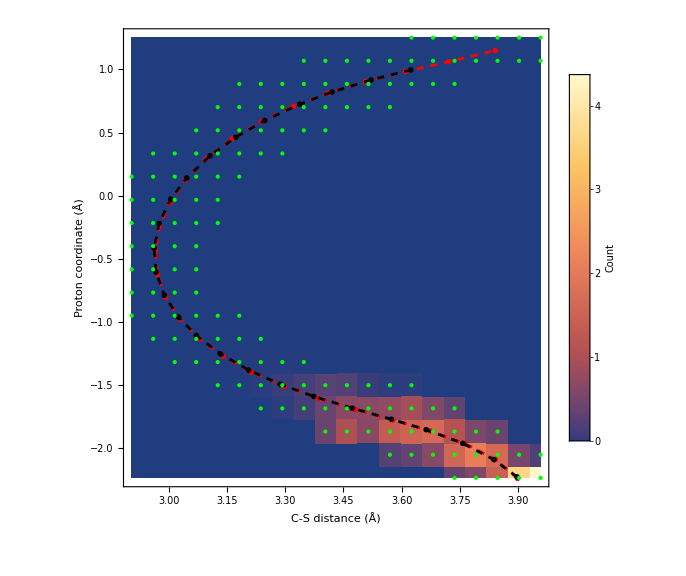

```mathematica
(*ρ2Dr12r3Jiayun=MapAt[If[#>10^3,0.,#]&,Table[{ρ2Dr12r3⟦i,2⟧,ρ2Dr12r3⟦i,1⟧,ρ2Dr12r3⟦i,3⟧},{i,1,Length[ρ2Dr12r3]}],{All,3}];*)
ρ2Dr12r3Jiayun=Table[{ρ2Dr12r3⟦i,2⟧,ρ2Dr12r3⟦i,1⟧,ρ2Dr12r3⟦i,3⟧},{i,1,Length[ρ2Dr12r3]}];
finalNewString2DmixJiayun=Reverse[finalNewString2Dmix[{1,-1,0},{0,0,1}],2];
finalNewStringExtended2DmixJiayun=Reverse[finalNewStringExtended2Dmix[{1,-1,0},{0,0,1}],2];
lowCountBins=Select[ρ2Dr12r3Jiayun,0<#⟦3⟧<50&]⟦All,{1,2}⟧;
Show[
ListDensityPlot[ρ2Dr12r3Jiayun,
Mesh->None,InterpolationOrder->0,PlotRange->All,
ImageSize->Large,
FrameStyle->Directive[Black,Thickness[0.003]],
BaseStyle->{FontSize->20,FontFamily->"Lato"},FrameLabel->{"C-S distance (Å)","Proton coordinate (Å)" },
PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{10,0},LegendLabel->"Count",LabelStyle->{FontFamily->"Lato",18},LegendMarkerSize->500],Right],
ClippingStyle->White,
Epilog->{Green,PointSize->Large,Point[lowCountBins]}
],
ListPlot[finalNewStringExtended2DmixJiayun,Joined->True,PlotMarkers->{"OpenMarkers",Medium},PlotStyle->{Red,Dashed}],
ListPlot[finalNewString2DmixJiayun,Joined->True,PlotMarkers->{"OpenMarkers",Medium},PlotStyle->{Black,Dashed}]
]
```

For example (takes some time, maybe 3-5 minutes, be patient)

```mathematica
F2Dmixr12r3=F2Dmix[{1,-1,0},{0,0,1}];//EchoTiming
```

Fmin: (-2.23716,3.95751) → -0.879234 kcal/mol (4.37028 weighted hits)

186.557

```mathematica
F2Dmixr12r3clean=Select[F2Dmixr12r3,VectorQ[#,NumberQ[N[#]]&]&];
F2Dmixr12r3high=F2Dmixr12r3/.{Indeterminate->999};
```

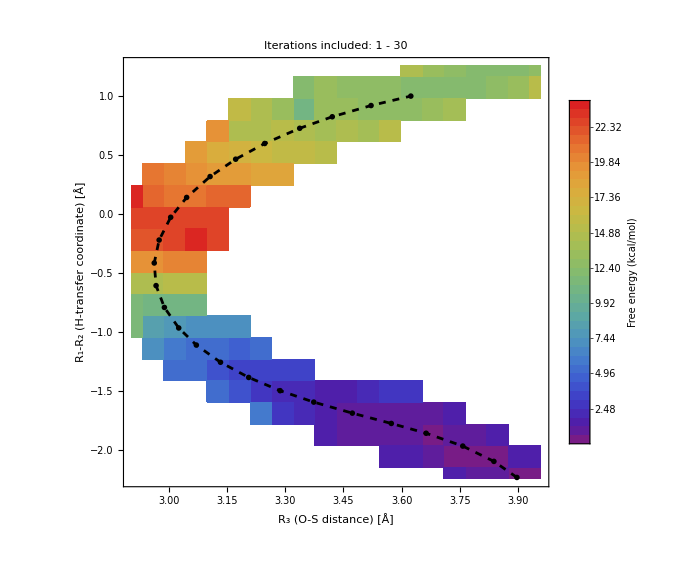

```mathematica
F2Dmixr12r3jiayun=Table[{F2Dmixr12r3⟦i,2⟧,F2Dmixr12r3⟦i,1⟧,F2Dmixr12r3⟦i,3⟧},{i,1,Length[F2Dmixr12r3]}];
finalNewString2DmixJiayun=Reverse[finalNewString2Dmix[{1,-1,0},{0,0,1}],2];
Show[
ListContourPlot[F2Dmixr12r3jiayun,
PlotLabel->"Iterations included: "<>ToString[iterationsSelected⟦1⟧]<>" - "<>ToString[iterationsSelected⟦-1⟧]<>"\n",
PlotRange->{0,32},
ContourStyle->None,
Contours->50,
ContourShading->Automatic,
PerformanceGoal->"Quality",
MaxPlotPoints->100,
ColorFunction->"Rainbow",
ClippingStyle->None,
InterpolationOrder->0,
LabelStyle->Directive[Black,18],
ImageSize->Large,
FrameStyle->Directive[Black,Thickness[0.0015]],
BaseStyle->{FontSize->18,FontFamily->"Lato"},FrameLabel->{"R_3 (O-S distance) [Å]","R_1-R_2 (H-transfer coordinate) [Å]" },
PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{10,0},LegendLabel->"\nFree energy\n(kcal/mol)",LabelStyle->{FontFamily->"Lato",16},LegendMarkerSize->500],Right]
],
ListPlot[finalNewString2DmixJiayun,Joined->True,PlotMarkers->{"OpenMarkers",Medium},PlotStyle->{Black,Dashed}]
]
```

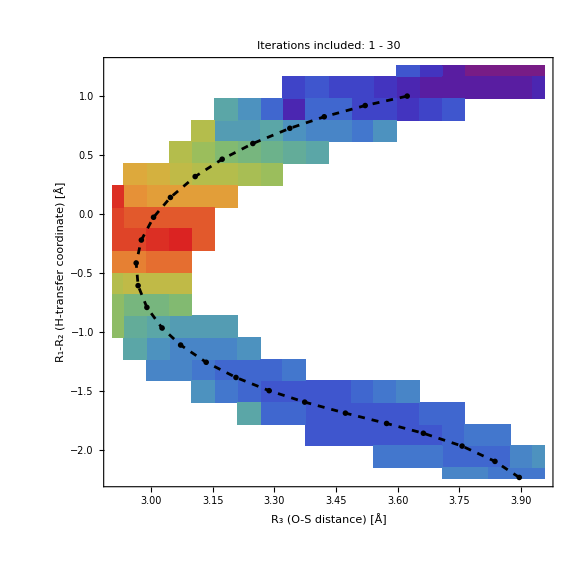

```mathematica
Select[F2Dmixr12r3jiayun[[All,3]],#==0&]
```

{0.}

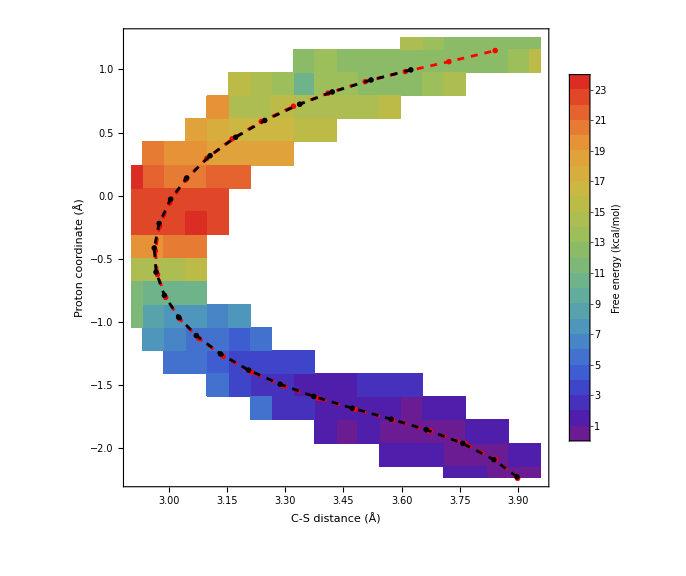

```mathematica
F2Dmixr12r3jiayun=Table[{F2Dmixr12r3high⟦i,2⟧,F2Dmixr12r3high⟦i,1⟧,F2Dmixr12r3high⟦i,3⟧},{i,1,Length[F2Dmixr12r3high]}];
finalNewStringExtended2DmixJiayun=Reverse[finalNewStringExtended2Dmix[{1,-1,0},{0,0,1}],2];
Show[
ListContourPlot[F2Dmixr12r3jiayun,
(*PlotLabel->"Iterations included: "<>ToString[iterationsSelected⟦1⟧]<>" - "<>ToString[iterationsSelected⟦-1⟧]<>"\n",*)
PlotRange->{-20,32},
ContourStyle->None,
Contours->50,
ContourShading->Automatic,
PerformanceGoal->"Quality",
MaxPlotPoints->100,
ColorFunction->"Rainbow",
ClippingStyle->None,
InterpolationOrder->0,
LabelStyle->Directive[Black,24],
ImageSize->Large,
FrameStyle->Directive[Black,Thickness[0.003]],
BaseStyle->{FontSize->24,FontFamily->"Lato"},FrameLabel->{"C-S distance (Å)","Proton coordinate (Å)" },
PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{10,0},LegendLabel->"Free energy\n(kcal/mol)",LabelStyle->{FontFamily->"Lato",16},LegendMarkerSize->500],Right]
],
ListPlot[finalNewStringExtended2DmixJiayun,Joined->True,PlotMarkers->{"OpenMarkers",Medium},PlotStyle->{Red,Dashed}],
ListPlot[finalNewString2DmixJiayun,Joined->True,PlotMarkers->{"OpenMarkers",Medium},PlotStyle->{Black,Dashed}]
]
```

## PMF along the final string

#### Multidimensional (ncoord) PMF

Final smooth strings with evenly distributed images

```mathematica
Monitor[
feFinalString=Block[{bspecImage,histogramImage,hitsImage,feImage,femin=6.023*10^23,felist={},time=0,timeperImage=0},
Do[
time=TimeUsed[];
bspecImage=Table[
{{finalString⟦image,icoord⟧-binwidth⟦icoord⟧/2,finalString⟦image,icoord⟧+binwidth⟦icoord⟧/2}},
{icoord,1,ncoord}];
histogramImage=HistogramList[weighteddataAll,bspecImage];
hitsImage=Flatten[histogramImage⟦2⟧]⟦1⟧;
feImage=-1/β Log[hitsImage];
If[feImage<femin,femin=feImage];
AppendTo[felist,feImage];
timeperImage=TimeUsed[]-time,
{image,1,nimageslast}
];
felist-femin
],
Panel@Grid[{
{"(Final string) Image",ProgressIndicator[image,{1,nimageslast}],image-1,"Weighted Counts"->hitsImage,"Time per image"->timeperImage,"sec"}
},Alignment->Automatic,Spacings->1]
];
Monitor[
feFinalNewString=Block[{bspecImage,histogramImage,hitsImage,feImage,femin=6.023*10^23,felist={},time=0,timeperImage=0},
Do[
time=TimeUsed[];
bspecImage=Table[
{{finalNewString⟦image,icoord⟧-binwidth⟦icoord⟧/2,finalNewString⟦image,icoord⟧+binwidth⟦icoord⟧/2}},
{icoord,1,ncoord}];
histogramImage=HistogramList[weighteddataAll,bspecImage];
hitsImage=Flatten[histogramImage⟦2⟧]⟦1⟧;
feImage=-1/β Log[hitsImage];
If[feImage<femin,femin=feImage];
AppendTo[felist,feImage];
timeperImage=TimeUsed[]-time,
{image,1,nimageslast}
];
felist-femin
],
Panel@Grid[{
{"(Final new string) Image",ProgressIndicator[image,{1,nimageslast}],image-1,"Weighted Counts"->hitsImage,"Time per image"->timeperImage,"sec"}
},Alignment->Automatic,Spacings->1]
];
```

```mathematica
binwidth
```

{0.08293,0.108145,0.055295}

```mathematica
Monitor[
feFinalNewStringExtended=Block[{bspecImage,histogramImage,hitsImage,feImage,femin=6.023*10^23,felist={},time=0,timeperImage=0,nimageslast},
nimageslast=Length[finalNewStringExtended];
Do[
time=TimeUsed[];
bspecImage=Table[
{{finalNewStringExtended⟦image,icoord⟧-binwidth⟦icoord⟧/2,finalNewStringExtended⟦image,icoord⟧+binwidth⟦icoord⟧/2}},
{icoord,1,ncoord}];
histogramImage=HistogramList[weighteddataAll,bspecImage];
hitsImage=Flatten[histogramImage⟦2⟧]⟦1⟧;
(*Print["Image: ",image,"  Bin:",bspecImage,"   Hits: ",hitsImage];*)
feImage=-1/β Log[hitsImage];
If[feImage<femin,femin=feImage];
AppendTo[felist,feImage];
timeperImage=TimeUsed[]-time,
{image,1,nimageslast}
];
felist-femin
],
Panel@Grid[{
{"Image",ProgressIndicator[image,{1,nimageslast}],image-1,"Weighted Counts"->hitsImage,"Time per image"->timeperImage,"sec"}
},Alignment->Automatic,Spacings->1]
];
```

```mathematica
feFinalString
```

{0.218744,0.,0.056239,0.271979,0.436264,0.736026,1.24127,1.94233,2.8605,4.00421,5.53754,7.46053,10.0318,14.5313,19.695,21.9582,21.9387,20.0728,18.5422,16.8637,15.4,14.1229,13.1475,12.3435,11.8322}

```mathematica
feFinalNewString
```

{0.247882,0.,0.0334275,0.249669,0.339033,0.693084,1.14462,1.89147,2.7502,3.84137,5.29874,7.20564,9.63587,14.1208,19.2419,21.8447,21.9269,20.5341,18.6666,17.0234,15.4709,14.2036,13.1814,12.3184,11.7772}

```mathematica
finalNewStringExtended
```

{{1.07076,3.31121,3.89831},{1.10092,3.19146,3.84086},{1.11436,3.08022,3.76345},{1.11374,2.97816,3.67307},{1.10475,2.88174,3.57703},{1.09281,2.78633,3.48021},{1.08217,2.6883,3.38582},{1.07616,2.58544,3.29639},{1.07747,2.47671,3.21403},{1.08826,2.36218,3.14075},{1.11027,2.24287,3.07836},{1.14468,2.12074,3.02856},{1.19224,1.99819,2.99264},{1.25322,1.87805,2.97165},{1.32721,1.76375,2.9663},{1.41329,1.6586,2.97689},{1.5097,1.56592,3.00313},{1.61404,1.48843,3.04411},{1.72337,1.4278,3.09832},{1.83473,1.38443,3.16385},{1.94534,1.35738,3.23873},{2.05307,1.34464,3.32138},{2.15615,1.34335,3.41072},{2.25308,1.3497,3.50642},{2.34221,1.35806,3.60937},{2.4197,1.35773,3.7214},{2.47343,1.32359,3.8406}}

```mathematica
feFinalNewStringExtended
```

{0.299402,0.,0.0214612,0.209302,0.319109,0.676211,1.13303,1.84422,2.65006,3.67588,5.01672,7.07584,9.30175,13.6062,18.6425,21.7029,21.9553,20.6959,18.8389,17.1918,15.631,14.4657,13.2324,12.4864,11.8685,11.4437,12.64}

Final string with images obtained at the last iteration:

```mathematica
Monitor[
feFinalReq=Block[{bspecImage,histogramImage,hitsImage,feImage,femin=6.023*10^23,felist={},time=0,timeperImage=0},
Do[
time=TimeUsed[];
bspecImage=Table[
{{finalReq⟦image,icoord⟧-binwidth⟦icoord⟧/2,finalReq⟦image,icoord⟧+binwidth⟦icoord⟧/2}},
{icoord,1,ncoord}];
histogramImage=HistogramList[weighteddataAll,bspecImage];
hitsImage=Flatten[histogramImage⟦2⟧]⟦1⟧;
feImage=-1/β Log[hitsImage];
If[feImage<femin,femin=feImage];
AppendTo[felist,feImage];
timeperImage=TimeUsed[]-time,
{image,1,nimageslast}
];
felist-femin
],
Panel@Grid[{
{"Image",ProgressIndicator[image,{1,nimageslast}],image-1,"Hits"->hitsImage,"Time per image"->timeperImage,"sec"}
},Alignment->Automatic,Spacings->1]
];
```

#### Projected 2D PMF for any two linear combinations of coordinates

Final smooth string with evenly distributed images

```mathematica
F2DfinalString[coef1_,coef2_]:=Module[{bspecImage,data2D,weighteddata2D,histogramImage,hitsImage,feImage,femin=6.023*10^23,felist={},binw1,binw2},
binw1=gGridmix[coef1]⟦2⟧-gGridmix[coef1]⟦1⟧;
binw2=gGridmix[coef2]⟦2⟧-gGridmix[coef2]⟦1⟧;
Do[
bspecImage=
{
{{Sum[coef1⟦icoord⟧finalString⟦image,icoord⟧,{icoord,1,ncoord}]-binw1/2,
Sum[coef1⟦icoord⟧finalString⟦image,icoord⟧,{icoord,1,ncoord}]+binw1/2}},
{{Sum[coef2⟦icoord⟧finalString⟦image,icoord⟧,{icoord,1,ncoord}]-binw2/2,
Sum[coef2⟦icoord⟧finalString⟦image,icoord⟧,{icoord,1,ncoord}]+binw2/2}}
};
data2D=Table[{Sum[coef1⟦i1⟧dataAll⟦k,i1⟧,{i1,1,ncoord}],Sum[coef2⟦i2⟧dataAll⟦k,i2⟧,{i2,1,ncoord}]},{k,1,Length[dataAll]}];
weighteddata2D=WeightedData[data2D,Flatten@WHAMweights];
histogramImage=HistogramList[weighteddata2D,bspecImage];
hitsImage=Flatten[histogramImage⟦2⟧]⟦1⟧;
feImage=-1/β Log[hitsImage];
If[feImage<femin,femin=feImage];
AppendTo[felist,feImage],
{image,1,nimageslast}
];
felist-femin
];
```

```mathematica
F2DfinalNewStringExtended[coef1_,coef2_]:=Module[{bspecImage,data2D,weighteddata2D,histogramImage,hitsImage,feImage,femin=6.023*10^23,felist={},binw1,binw2,nimagesExtended},
nimagesExtended=Length[finalNewStringExtended];
binw1=gGridmix[coef1]⟦2⟧-gGridmix[coef1]⟦1⟧;
binw2=gGridmix[coef2]⟦2⟧-gGridmix[coef2]⟦1⟧;
Do[
bspecImage=
{
{{Sum[coef1⟦icoord⟧finalNewStringExtended⟦image,icoord⟧,{icoord,1,ncoord}]-binw1/2,
Sum[coef1⟦icoord⟧finalNewStringExtended⟦image,icoord⟧,{icoord,1,ncoord}]+binw1/2}},
{{Sum[coef2⟦icoord⟧finalNewStringExtended⟦image,icoord⟧,{icoord,1,ncoord}]-binw2/2,
Sum[coef2⟦icoord⟧finalNewStringExtended⟦image,icoord⟧,{icoord,1,ncoord}]+binw2/2}}
};
data2D=Table[{Sum[coef1⟦i1⟧dataAll⟦k,i1⟧,{i1,1,ncoord}],Sum[coef2⟦i2⟧dataAll⟦k,i2⟧,{i2,1,ncoord}]},{k,1,Length[dataAll]}];
weighteddata2D=WeightedData[data2D,Flatten@WHAMweights];
histogramImage=HistogramList[weighteddata2D,bspecImage];
hitsImage=Flatten[histogramImage⟦2⟧]⟦1⟧;
feImage=-1/β Log[hitsImage];
If[feImage<femin,femin=feImage];
AppendTo[felist,feImage],
{image,1,nimagesExtended}
];
felist-femin
];
```

Final string with images obtained at the last iteration:

```mathematica
F2DfinalReq[coef1_,coef2_]:=Module[{bspecImage,data2D,weighteddata2D,histogramImage,hitsImage,feImage,femin=6.023*10^23,felist={},binw1,binw2},
binw1=gGridmix[coef1]⟦2⟧-gGridmix[coef1]⟦1⟧;
binw2=gGridmix[coef2]⟦2⟧-gGridmix[coef2]⟦1⟧;
Do[
bspecImage=
{
{{Sum[coef1⟦icoord⟧finalReq⟦image,icoord⟧,{icoord,1,ncoord}]-binw1/2,
Sum[coef1⟦icoord⟧finalReq⟦image,icoord⟧,{icoord,1,ncoord}]+binw1/2}},
{{Sum[coef2⟦icoord⟧finalReq⟦image,icoord⟧,{icoord,1,ncoord}]-binw2/2,
Sum[coef2⟦icoord⟧finalReq⟦image,icoord⟧,{icoord,1,ncoord}]+binw2/2}}
};
data2D=Table[{Sum[coef1⟦i1⟧dataAll⟦k,i1⟧,{i1,1,ncoord}],Sum[coef2⟦i2⟧dataAll⟦k,i2⟧,{i2,1,ncoord}]},{k,1,Length[dataAll]}];
weighteddata2D=WeightedData[data2D,Flatten@WHAMweights];
histogramImage=HistogramList[weighteddata2D,bspecImage];
hitsImage=Flatten[histogramImage⟦2⟧]⟦1⟧;
feImage=-1/β Log[hitsImage];
If[feImage<femin,femin=feImage];
AppendTo[felist,feImage],
{image,1,nimageslast}
];
felist-femin
];
```

#### Plots...

```mathematica
F2Dstring12=F2DfinalString[{1,0,0},{0,1,0}];//EchoTiming
F2Dstring13=F2DfinalString[{1,0,0},{0,0,1}];//EchoTiming
F2Dstring23=F2DfinalString[{0,1,0},{0,0,1}];//EchoTiming
F2Dstring123=F2DfinalString[{1,-1,0},{0,0,1}];//EchoTiming
F2DstringExtended12=F2DfinalNewStringExtended[{1,0,0},{0,1,0}];//EchoTiming
F2DstringExtended13=F2DfinalNewStringExtended[{1,0,0},{0,0,1}];//EchoTiming
F2DstringExtended23=F2DfinalNewStringExtended[{0,1,0},{0,0,1}];//EchoTiming
F2DstringExtended123=F2DfinalNewStringExtended[{1,-1,0},{0,0,1}];//EchoTiming
```

37.2432

36.1501

35.9125

35.7556

38.4156

38.2281

38.0317

37.9564

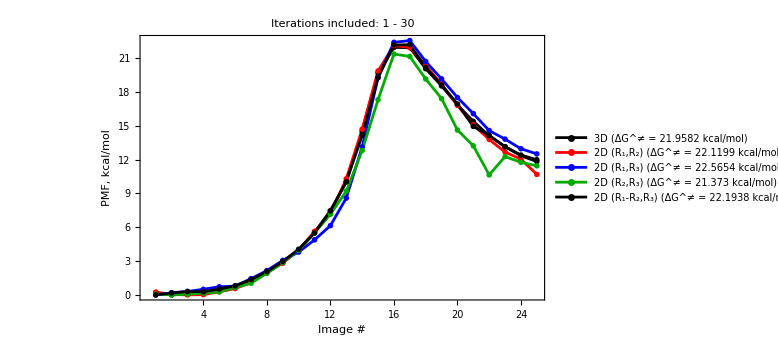

```mathematica
ListLinePlot[
{feFinalString,
F2Dstring12,
F2Dstring13,
F2Dstring23,
F2Dstring123},
PlotRange->All,
Axes->False,
Frame->True,
BaseStyle->{FontFamily->"Lato"},
FrameStyle->Directive[Thick,Black,18],
FrameLabel->{"Image #","PMF, kcal/mol"},
PlotLabel->"Iterations included: "<>ToString[iterationsSelected⟦1⟧]<>" - "<>ToString[iterationsSelected⟦-1⟧]<>"\n",
PlotMarkers->{"OpenMarkers",Medium},
ImageSize->Large,
LabelStyle->Directive[Black,FontSize->12],
PlotStyle->{
Black,
Red,
Blue,
Darker[Green]
},
PlotLegends->Placed[{
ToString[ncoord]<>"D (ΔG^≠ = "<>ToString[Max[feFinalString]-Min[feFinalString⟦1;;7⟧]]<>" kcal/mol)",
"2D (R_1,R_2) (ΔG^≠ = "<>ToString[Max[F2Dstring12]-Min[F2Dstring12⟦1;;7⟧]]<>" kcal/mol)",
"2D (R_1,R_3) (ΔG^≠ = "<>ToString[Max[F2Dstring13]-Min[F2Dstring13⟦1;;7⟧]]<>" kcal/mol)",
"2D (R_2,R_3) (ΔG^≠ = "<>ToString[Max[F2Dstring23]-Min[F2Dstring23⟦1;;7⟧]]<>" kcal/mol)",
"2D (R_1-R_2,R_3) (ΔG^≠ = "<>ToString[Max[F2Dstring123]-Min[F2Dstring123⟦1;;7⟧]]<>" kcal/mol)"
},{0.30,0.77}]
]
```

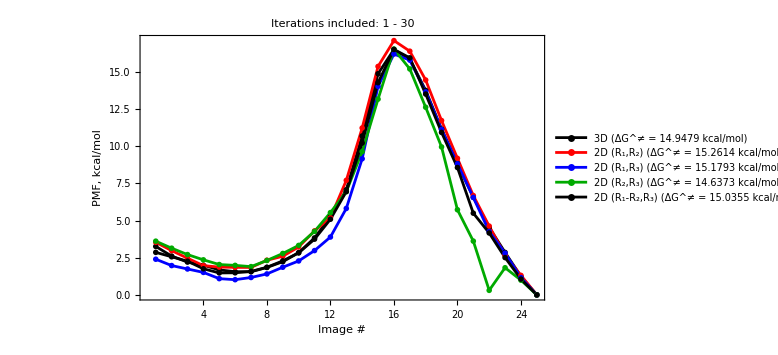

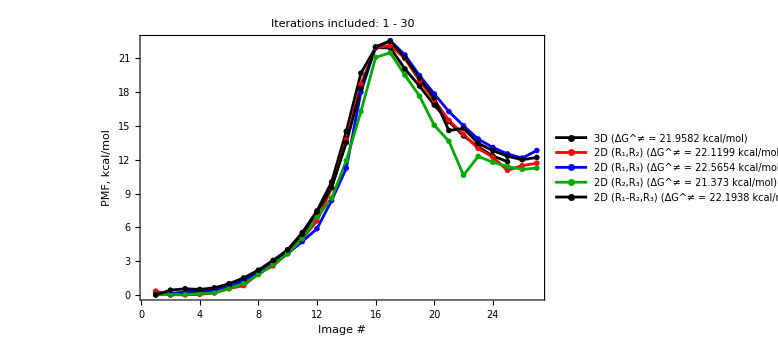

```mathematica
ListLinePlot[
{feFinalString,
F2DstringExtended12,
F2DstringExtended13,
F2DstringExtended23,
F2DstringExtended123},
PlotRange->All,
Axes->False,
Frame->True,
BaseStyle->{FontFamily->"Lato"},
FrameStyle->Directive[Thick,Black,18],
FrameLabel->{"Image #","PMF, kcal/mol"},
PlotLabel->"Iterations included: "<>ToString[iterationsSelected⟦1⟧]<>" - "<>ToString[iterationsSelected⟦-1⟧]<>"\n",
PlotMarkers->{"OpenMarkers",Medium},
ImageSize->Large,
LabelStyle->Directive[Black,FontSize->12],
PlotStyle->{
Black,
Red,
Blue,
Darker[Green]
},
PlotLegends->Placed[{
ToString[ncoord]<>"D (ΔG^≠ = "<>ToString[Max[feFinalString]-Min[feFinalString⟦1;;7⟧]]<>" kcal/mol)",
"2D (R_1,R_2) (ΔG^≠ = "<>ToString[Max[F2Dstring12]-Min[F2Dstring12⟦1;;7⟧]]<>" kcal/mol)",
"2D (R_1,R_3) (ΔG^≠ = "<>ToString[Max[F2Dstring13]-Min[F2Dstring13⟦1;;7⟧]]<>" kcal/mol)",
"2D (R_2,R_3) (ΔG^≠ = "<>ToString[Max[F2Dstring23]-Min[F2Dstring23⟦1;;7⟧]]<>" kcal/mol)",
"2D (R_1-R_2,R_3) (ΔG^≠ = "<>ToString[Max[F2Dstring123]-Min[F2Dstring123⟦1;;7⟧]]<>" kcal/mol)"
},{0.30,0.77}]
]
```

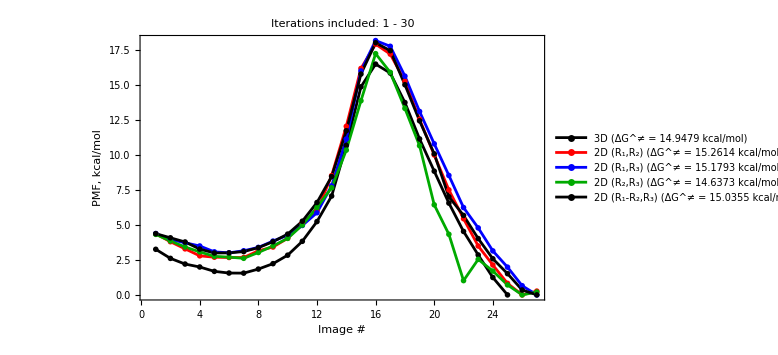

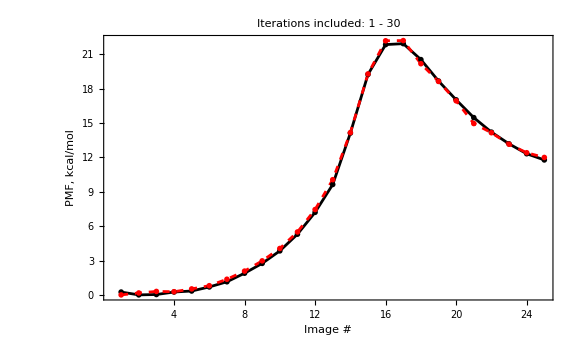

```mathematica
ListLinePlot[
{feFinalNewString,
F2Dstring123},
PlotRange->All,
Axes->False,
Frame->True,
BaseStyle->{14,FontFamily->"Lato"},
FrameStyle->Directive[Thick,Black,16],
FrameLabel->{"Image #","PMF, kcal/mol"},
PlotLabel->"Iterations included: "<>ToString[iterationsSelected⟦1⟧]<>" - "<>ToString[iterationsSelected⟦-1⟧]<>"\n",
PlotMarkers->{"OpenMarkers",Medium},
ImageSize->Large,
LabelStyle->Directive[Black,FontSize->14,TextAlignment->Left],
PlotStyle->{Black,{Red,Dashed}},
PlotLegends->Placed[{
ToString[ncoord]<>"D string\nΔG^≠ = "<>ToString[Max[feFinalNewString]-Min[feFinalNewString⟦1;;7⟧]]<>" kcal/mol\nΔG = "<>ToString[Min[feFinalString⟦15;;25⟧]-Min[feFinalString⟦1;;10⟧]]<>" kcal/mol",
"2D (R_1-R_2,R_3) string\nΔG^≠ = "<>ToString[Max[F2Dstring123]-Min[F2Dstring123⟦1;;7⟧]]<>" kcal/mol\nΔG = "<>ToString[Min[F2Dstring123⟦15;;25⟧]-Min[F2Dstring123⟦1;;10⟧]]<>" kcal/mol"
},{0.3,0.65}]
]
```

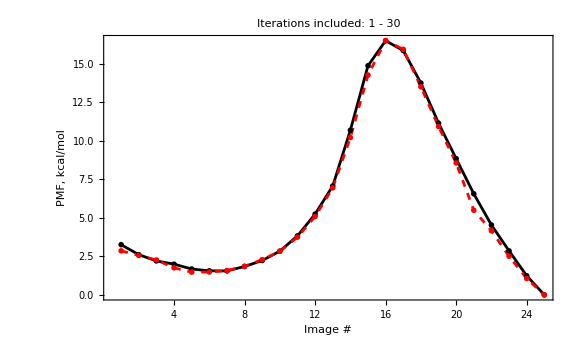

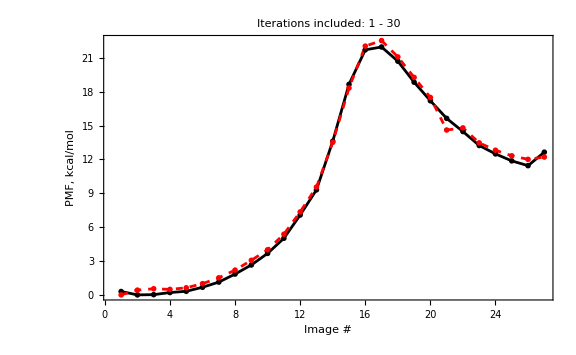

```mathematica
ListLinePlot[
{feFinalNewStringExtended,
F2DstringExtended123},
PlotRange->All,
Axes->False,
Frame->True,
BaseStyle->{14,FontFamily->"Lato"},
FrameStyle->Directive[Thick,Black,16],
FrameLabel->{"Image #","PMF, kcal/mol"},
PlotLabel->"Iterations included: "<>ToString[iterationsSelected⟦1⟧]<>" - "<>ToString[iterationsSelected⟦-1⟧]<>"\n",
PlotMarkers->{"OpenMarkers",Medium},
ImageSize->Large,
LabelStyle->Directive[Black,FontSize->14,TextAlignment->Left],
PlotStyle->{Black,{Red,Dashed}},
PlotLegends->Placed[{
ToString[ncoord]<>"D string\nΔG^≠ = "<>ToString[Max[feFinalStringExtended]-Min[feFinalStringExtended⟦1;;7⟧]]<>" kcal/mol\nΔG = "<>ToString[Min[feFinalStringExtended⟦15;;27⟧]-Min[feFinalStringExtended⟦1;;10⟧]]<>" kcal/mol",
"2D (R_1-R_2,R_3) string\nΔG^≠ = "<>ToString[Max[F2DstringExtended123]-Min[F2DstringExtended123⟦1;;7⟧]]<>" kcal/mol\nΔG = "<>ToString[Min[F2DstringExtended123⟦15;;25⟧]-Min[F2DstringExtended123⟦1;;10⟧]]<>" kcal/mol"
},{0.3,0.65}]
]
```

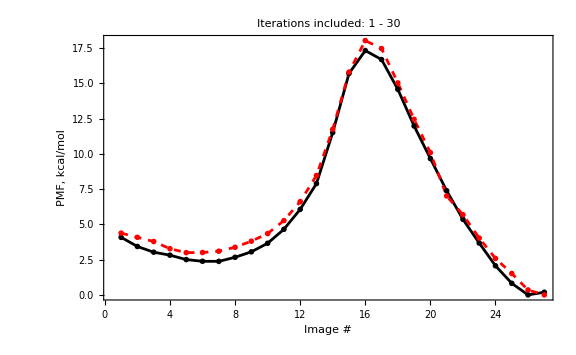

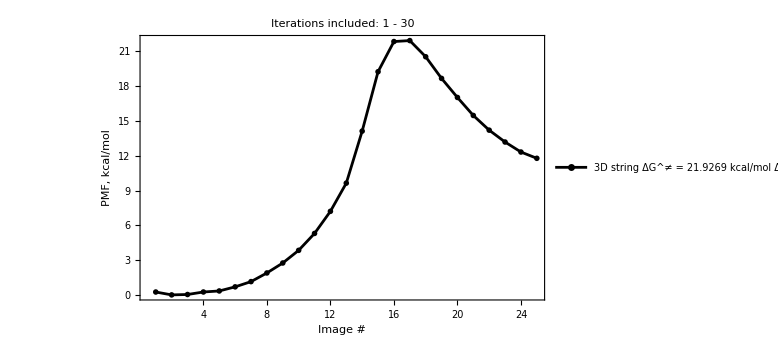

```mathematica
ListLinePlot[
{feFinalNewString},
PlotRange->All,
Axes->False,
Frame->True,
BaseStyle->{14,FontFamily->"Lato"},
FrameStyle->Directive[Thick,Black,16],
FrameLabel->{"Image #","PMF, kcal/mol"},
PlotLabel->"Iterations included: "<>ToString[iterationsSelected⟦1⟧]<>" - "<>ToString[iterationsSelected⟦-1⟧]<>"\n",
PlotMarkers->{"OpenMarkers",Medium},
ImageSize->Large,
LabelStyle->Directive[Black,FontSize->14,TextAlignment->Left],
PlotStyle->{Black,{Red,Dashed},{Blue,Dashed}},
PlotLegends->Placed[{
ToString[ncoord]<>"D string\nΔG^≠ = "<>ToString[Max[feFinalNewString]-Min[feFinalNewString⟦1;;7⟧]]<>" kcal/mol\nΔG = "<>ToString[Min[feFinalNewString⟦15;;25⟧]-Min[feFinalNewString⟦1;;7⟧]]<>" kcal/mol"
},{0.3,0.65}]
]
```

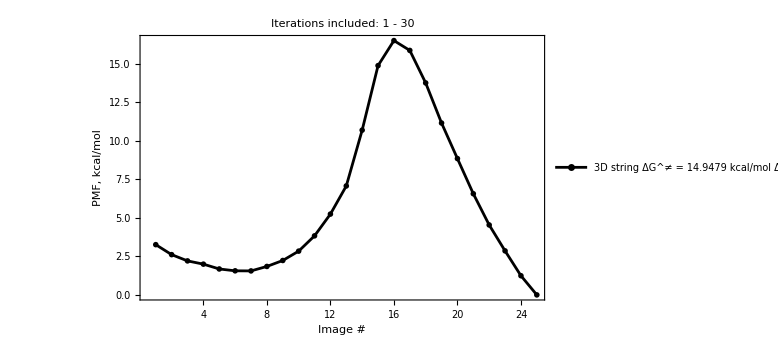

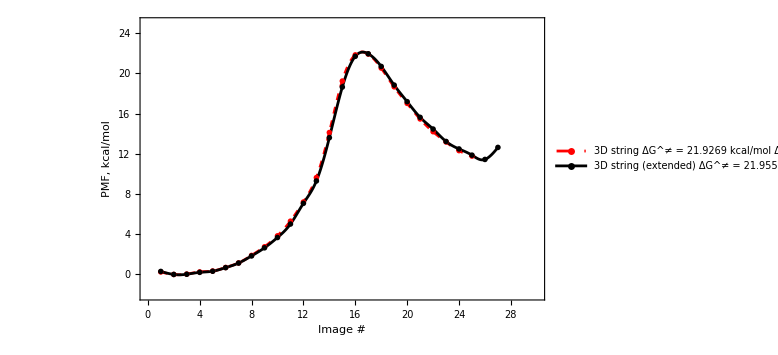

```mathematica
ListLinePlot[
{feFinalNewString,feFinalNewStringExtended},
PlotRange->{{0,30},{-2,25}},
InterpolationOrder->3,
Axes->False,
Frame->True,
BaseStyle->{18,FontFamily->"Lato"},
FrameStyle->Directive[Thick,Black,18],
FrameLabel->{"Image #","PMF, kcal/mol"},
(*PlotLabel->"Iterations included: "<>ToString[iterationsSelected⟦1⟧]<>" - "<>ToString[iterationsSelected⟦-1⟧]<>"\n",*)
PlotMarkers->{"OpenMarkers",Medium},
ImageSize->Large,
LabelStyle->Directive[Black,FontSize->16,TextAlignment->Left],
PlotStyle->{{Red,Dashed},Black,{Blue,Dashed}},
PlotLegends->Placed[{
ToString[ncoord]<>"D string\nΔG^≠ = "<>ToString[Max[feFinalNewString]-Min[feFinalNewString⟦1;;15⟧]]<>" kcal/mol\nΔG = "<>ToString[Min[feFinalNewString⟦15;;25⟧]-Min[feFinalNewString⟦1;;15⟧]]<>" kcal/mol",
ToString[ncoord]<>"D string (extended)\nΔG^≠ = "<>ToString[Max[feFinalNewStringExtended]-Min[feFinalNewStringExtended⟦1;;15⟧]]<>" kcal/mol\nΔG = "<>ToString[Min[feFinalNewStringExtended⟦15;;27⟧]-Min[feFinalNewStringExtended⟦1;;15⟧]]<>" kcal/mol"
},{0.25,0.75}]
]
```

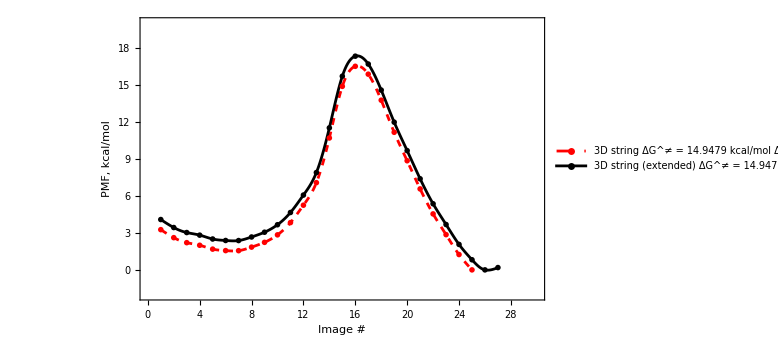

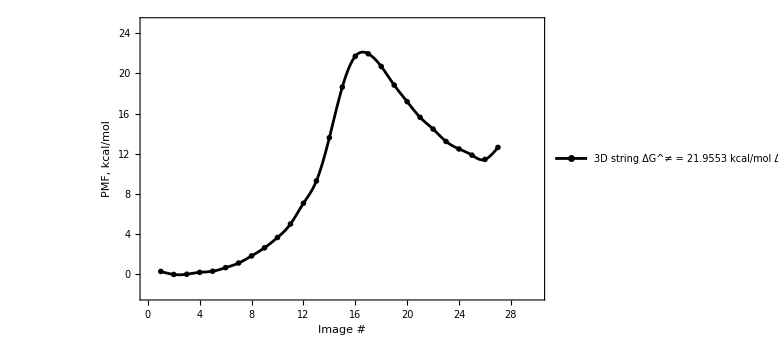

```mathematica
ListLinePlot[
{feFinalNewStringExtended},
PlotRange->{{0,30},{-2,25}},
InterpolationOrder->3,
Axes->False,
Frame->True,
BaseStyle->{18,FontFamily->"Lato"},
FrameStyle->Directive[Thick,Black,18],
FrameLabel->{"Image #","PMF, kcal/mol"},
(*PlotLabel->"Iterations included: "<>ToString[iterationsSelected⟦1⟧]<>" - "<>ToString[iterationsSelected⟦-1⟧]<>"\n",*)
PlotMarkers->{"OpenMarkers",Medium},
ImageSize->Large,
LabelStyle->Directive[Black,FontSize->16,TextAlignment->Left],
PlotStyle->{Black,{Red,Dashed},{Blue,Dashed}},
PlotLegends->Placed[{
ToString[ncoord]<>"D string\nΔG^≠ = "<>ToString[Max[feFinalNewStringExtended]-Min[feFinalNewStringExtended⟦1;;15⟧]]<>" kcal/mol\nΔG = "<>ToString[Min[feFinalNewStringExtended⟦15;;27⟧]-Min[feFinalNewStringExtended⟦1;;15⟧]]<>" kcal/mol"
},{0.25,0.85}]
]
```

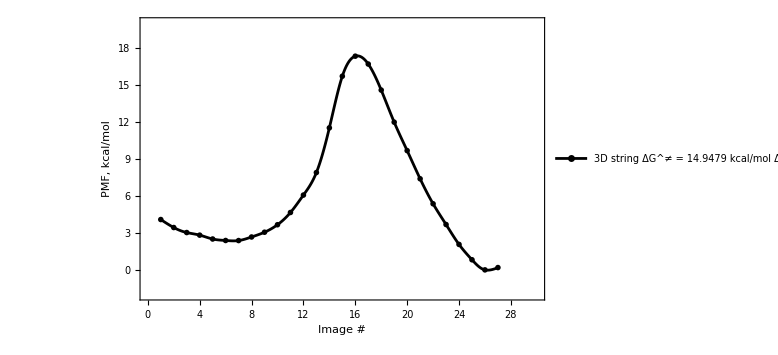

## And lastly...

```mathematica
word=Rasterize[Graphics[{Text[Style["Winter is coming...",Bold,40]]}],"Image"];
text=ColorNegate[ImagePad[ImageCrop[word],15,White]];
stack=Image3D@Join[ConstantArray[text,20],ConstantArray[ColorConvert[ConstantImage[1,ImageDimensions[text]],"RGB"],15]];
ImageMesh[stack,Method->"DualMarchingCubes"]
```

-Graphics3D-